## Basics

```mathematica
ReadGrof[n_]:=Block[{fileName,l,f, str},
fileName = "D:\\saved\\Grofs\\"<> ToString[n] <> ".grof";
f=OpenRead[fileName,BinaryFormat->False];
l=ReadList[f,"String",1,RecordSeparators->{"\r\n","\r" }];
l="{"<>l[[1]]<>"}";
str=StringToStream[l];
l=ReadList[str,Expression,1];
Close[str];
Close[f];
Return[Graph[l[[1]]]]
]
```

```mathematica
ReadFaces[n_]:=Block[{fileName,l,f,line, result, lines},
result={};
fileName = "D:\\Grofs\\Faces\\"<> ToString[n] <> ".face";
lines=ReadList[fileName,Record];
result=Map[
With[{str=StringToStream["{"<>#<>"}"]},
l=ReadList[str,Expression][[1]];
Close[str];
l
]&,lines];
(* first item is face id, then 3 vertices of the face, then the face ids of the neighbours *)
result=Map[Take[#,{2,4}]&,result];
Return[result]
]
```

```mathematica
ReadGraphDiamond[n_]:=Block[
{f, l},
f=OpenRead["d:\\grofs\\diamonds\\"<>ToString[n]<>".diamond"];
l=ReadList[f,"String",1,RecordSeparators->{"\r\n","\r" }];
Close[f];
l="{"<>l[[1]]<>"}";
l=ReadList[StringToStream[l],Expression,1];
Return[l[[1]]]
]
```

```mathematica
ReadGraphDiamondHighLights[n_]:=Block[
{f, l, result, chunk, colors =ColorData[109,"ColorList"], i},
result={};
f=OpenRead["d:\\grofs\\diamonds\\"<>ToString[n]<>".diamond"];
l=ReadList[f,"String",20,RecordSeparators->{"\r\n","\r" }];
result=Table[Read[StringToStream["{"<>k<>"}"]],{k,l}];
result=Table[Style[result[[i]],Thick,colors[[i]]],{i,1,Length[result]}];
Close[f];
Return[result]
]
```

```mathematica
CloseAll[]:=Map[Close[#]&,Cases[Streams[],_InputStream]]
```

```mathematica
DefineOrLoad[symbol_,op_]:=Block[{fileName="d:\\saved\\symbols\\"<> symbol<>".m",result},
If[FileExistsQ[fileName],
Print["Loading ", fileName];
result=Get[fileName],
result=op[];
Put[result,fileName];
Print["Saved ", fileName];
];
result
]
```

## Bounds

```mathematica
Jacobsthal=LinearRecurrence[{2,1,-2},{0,2,1},50]
```

{0,2,1,4,5,12,21,44,85,172,341,684,1365,2732,5461,10924,21845,43692,87381,174764,349525,699052,1398101,2796204,5592405,11184812,22369621,44739244,89478485,178956972,357913941,715827884,1431655765,2863311532,5726623061,11453246124,22906492245,45812984492,91625968981,183251937964,366503875925,733007751852,1466015503701,2932031007404,5864062014805,11728124029612,23456248059221,46912496118444,93824992236885,187649984473772}

```mathematica
CountMPG={2,2,5,14,50,233,1249,7595,49566,339722}
```

{2,2,5,14,50,233,1249,7595,49566,339722}

```mathematica
EndMPG=Accumulate[CountMPG]
```

{2,4,9,23,73,306,1555,9150,58716,398438}

```mathematica
StartMpg=Join[{1},EndMPG+1]
```

{1,3,5,10,24,74,307,1556,9151,58717,398439}

```mathematica
mpgBounds=Table[{StartMpg[[k]],EndMPG[[k]]},{k,1,9}]
```

{{1,2},{3,4},{5,9},{10,23},{24,73},{74,306},{307,1555},{1556,9150},{9151,58716}}

## Colofouring

```mathematica
Chromial[n_]:=Chromial[n]=ChromaticPolynomial[ReadGrof[n],x]
```

```mathematica
Chrom[n_]:=Chrom[n]=ChromaticPolynomial[ReadGrof[n],4]
```

```mathematica
Get["D:\\pre398438.m"];Length[pre];Table[Chrom[k]=pre[[k]],{k,1,Length[pre]}];"DONE"
```

Get::noopen: Cannot open D:\pre398438.m.

DONE

```mathematica
chroms=Keys[Get["d:\\chroms.m"]];Length[chroms]
```

Get::noopen: Cannot open d:\chroms.m.

Keys::invrl: The argument $Failed is not a valid Association or a list of rules.

1

```mathematica
(*Table[
pre=Monitor[Table[Chrom[k],{k,1,max}],{k,N[k/max * 100]}];
Print["Saving D:\\pre-" <> ToString[max]<> ".txt"];
Save["D:\\pre" <> ToString[max]<> ".m",{pre}]; Print[max];max,
{max,Range[265000,300000,5000]}
]*)
```

## Colofiving

```mathematica
Chrom5[n_]:=Chrom5[n]=ChromaticPolynomial[ReadGrof[n],5]
```

```mathematica
Get["D:\\five398438.m"];Length[five];Table[Chrom5[k]=five[[k]],{k,1,Length[five]}];"DONE"
```

Get::noopen: Cannot open D:\five398438.m.

DONE

```mathematica
(*Table[
five=Monitor[Table[Chrom5[k],{k,1,max}],{k,N[k/max * 100]}];
Print["Saving D:\\five" <> ToString[max]<> ".m"];
Save["D:\\five" <> ToString[max]<> ".m",{five}]; Print[max];max,
{max,Range[25000,100000,25000]}
]*)
```

```mathematica
MaxFive[n_]:=(-5 (-1)^n+2^(1+n)+5 3^n)/12
```

## ColoThree

```mathematica
Chrom3[n_]:=Chrom3[n]=ChromaticPolynomial[ReadGrof[n],3]
```

```mathematica
Get["D:\\three398438.m"];Length[three];Table[Chrom3[k]=three[[k]],{k,1,Length[three]}];"DONE"
```

Get::noopen: Cannot open D:\three398438.m.

DONE

```mathematica
(*Table[
five=Monitor[Table[Chrom5[k],{k,1,max}],{k,N[k/max * 100]}];
Print["Saving D:\\five" <> ToString[max]<> ".m"];
Save["D:\\five" <> ToString[max]<> ".m",{five}]; Print[max];max,
{max,Range[25000,100000,25000]}
]*)
```

```mathematica
MaxFive[n_]:=(-5 (-1)^n+2^(1+n)+5 3^n)/12
```

## Rules

```mathematica
Rule1[g_,v1_, v2_,v3_]:= Block[{new, result=g},
new=Max[VertexList[g]]+1;
result=EdgeAdd[result,{v1<->new,v2<->new,v3<->new}];
result]
```

```mathematica
Rule2[g_,e_, e2_]:= Block[{new, result, start = e[[1]], stop=e[[2]], start2 = e2[[1]], stop2=e2[[2]]},
new=Max[VertexList[g]]+1;
result=EdgeDelete[g,e];
result=VertexAdd[result,new];
result=EdgeAdd[result,{start<->new,stop<->new,start2<->new,stop2<->new}];
result]
```

```mathematica
Rule3[g_,edges_,circle_]:=Block[{result,newNode},
newNode=Max[VertexList[g]]+1;
result=EdgeDelete[g,edges];
result=EdgeAdd[result,Table[v<->newNode,{v,circle}]];
result
]
```

## Reductions

```mathematica
ContainsRule1Reduction[n_]:= ContainsRule1Reduction[n]=Block[{interesting, found=False, g=ReadGrof[n]},
interesting=Table[v,{v,Select[VertexList[g],VertexDegree[g,#]==3&]}];
Table[If[MaximalPlanarQ[VertexDelete[g,v]],found=True],{v,interesting}];
Return [found]
]
```

```mathematica
redcount=ReadList["D:\\containsrule1red-50000.txt"];Length[redcount];Table[ContainsRule1Reduction[k]=redcount[[k]],{k,1,Length[redcount]}];"DONE"
```

ReadList::noopen: Cannot open D:\containsrule1red-50000.txt.

DONE

```mathematica
(*Table[
redcount=Monitor[Table[ContainsRule1Reduction[k],{k,1,max}],{k,N[k/max * 100]}];
PrintTemporary["Saving D:\\containsrule1red-" <> ToString[max]<> ".txt"];
Export["D:\\containsrule1red-" <> ToString[max]<> ".txt",redcount,"Table"]; Print[max];max,
{max,Range[1,58716,58716-1]}
]*)
```

## Drawing

```mathematica
ToVars[g_]:=Block[{exp,sep,vertex, vertices,var,var1, var2,  edges, edgeIndex, edge},
(* works only for graphs in which 1,2 and 3 are connected *)
exp= "Solve[";
sep="";
vertices=VertexList[g];
For[vertex=1,vertex<=Length[vertices], vertex++,
var ="x" <> ToString[ vertices[[vertex]] ];
exp= exp<>sep<> "Element["<>var<>", Integers]";
sep=" && " 
];

For[vertex=1,vertex<=Length[vertices], vertex++,
var ="x" <> ToString[ vertices[[vertex]] ];
exp= exp<>sep<> "(1<="<>var<>" <=4)";
sep=" && " 
];

edges=EdgeList[g];

exp= exp<>sep<> "x1 == 1 && x2== 2 && x3==3";
sep=" && " ;

For[edgeIndex=1,edgeIndex≤Length[edges],edgeIndex++,
edge=edges[[edgeIndex]];
var1 ="x" <> ToString[ edge[[1]] ];
var2 ="x" <> ToString[ edge[[2]] ];
exp= exp<>sep<> var1<>"!="<>var2;
sep=" && " 
];
exp=exp <> ", {";
sep="";
For[vertex=1,vertex<=Length[vertices], vertex++,
var ="x" <> ToString[ vertices[[vertex]] ];
exp= exp<>sep<> var;
sep=", " 
];
exp=exp <> "}]";
Return[Read[ StringToStream[ exp],Expression]]
]
```

```mathematica
ToEquations[g_]:=Block[{exp,vertex, vertices,var,var1, var2,  edges, edgeIndex, edge},
exp=True;
vertices=VertexList[g];
For[vertex=1,vertex<=Length[vertices], vertex++,
var =Symbol["x" <> ToString[ vertices[[vertex]] ]];
exp= exp&& Element[var, Integers];
];

For[vertex=1,vertex<=Length[vertices], vertex++,
var =Symbol["x" <> ToString[ vertices[[vertex]] ]];
exp= exp&& (1≤var <=4);
];

edges=EdgeList[g];

For[edgeIndex=1,edgeIndex≤Length[edges],edgeIndex++,
edge=edges[[edgeIndex]];
var1 =Symbol["x" <> ToString[ edge[[1]] ]];
var2 =Symbol["x" <> ToString[ edge[[2]] ]];
exp= exp&& var1!=var2;
];
exp
]
```

```mathematica
ToColors[l_]:=Block[{index, val, color, var, result},
result={};
For[index=1,index≤Length[l],index++,
var =ToExpression[ StringDrop [ToString[l[[index,1]]],1]];
color= IndexToColor [l[[index,2]] ];
AppendTo[result,var->color]
];
result
]
```

```mathematica
IndexToColor[i_]:={Red,Green,Blue, Yellow}[[i]]
```

```mathematica
ListToColor[l_]:=Map[IndexToColor[#]&,l]
```

```mathematica
ToColors2[assoc_]:=Map[#->IndexToColor[assoc[#]]&,Keys[assoc]]
```

```mathematica
PaintGraph[g_, opts__]:=Block[{sols},
sols=ToVars[g];
{Map[
VertexDelete[Graph[g,PlotLabel->ChromaticPolynomial[g,4],ImageSize->250, GraphLayout->"PlanarEmbedding", VertexStyle->ToColors[#], VertexLabels->"Name", VertexSize->Medium, opts],{1,2,3}]&
,sols],
Map[
Graph[g,PlotLabel->ChromaticPolynomial[g,4],ImageSize->250, GraphLayout->"PlanarEmbedding", VertexStyle->ToColors[#], VertexLabels->"Name", VertexSize->Medium, opts]&
,sols]}
]
```

## Drawing Part 2

```mathematica
ToVars2[g_, pre_]:=Block[{exp,sep,vertex, vertices,var,var1, var2,  edges, edgeIndex, edge},
exp= "Solve[";
sep="";
vertices=VertexList[g];
For[vertex=1,vertex<=Length[vertices], vertex++,
var ="x" <> ToString[ vertices[[vertex]] ];
exp= exp<>sep<> "Element["<>var<>", Integers]";
sep=" && " 
];

For[vertex=1,vertex<=Length[vertices], vertex++,
var ="x" <> ToString[ vertices[[vertex]] ];
exp= exp<>sep<> "(1<="<>var<>" <=4)";
sep=" && " 
];

edges=EdgeList[g];

exp= exp<>sep<> pre;(* "x1 == 1 && x2== 2 && x3==3";*)
sep=" && " ;

For[edgeIndex=1,edgeIndex≤Length[edges],edgeIndex++,
edge=edges[[edgeIndex]];
var1 ="x" <> ToString[ edge[[1]] ];
var2 ="x" <> ToString[ edge[[2]] ];
exp= exp<>sep<> var1<>"!="<>var2;
sep=" && " 
];
exp=exp <> ", {";
sep="";
For[vertex=1,vertex<=Length[vertices], vertex++,
var ="x" <> ToString[ vertices[[vertex]] ];
exp= exp<>sep<> var;
sep=", " 
];
exp=exp <> "}]";
Return[Read[ StringToStream[ exp],Expression]]
]
```

```mathematica
Criterion[edge1_,edge2_]:="x"<>ToString[edge1[[1]]]<>"==1&&x"<>ToString[edge1[[2]]]<>"==2&&x"<>ToString[edge2[[1]]]<>"==3"
```

```mathematica
PaintGraph2[g_,pre_, opts__]:=Block[{sols},
sols=ToVars2[g,pre];
Map[
Graph[
(*Print[Map[Last,ToColors[Sort[#]]]//Row];*)g,opts, GraphLayout->"PlanarEmbedding", VertexStyle->ToColors[#],  VertexSize->Medium]&
,sols]
]
```

```mathematica
GraphSolutions[g_,pre_]:=Block[{sols},
sols=ToVars2[g,pre];
Map[Map[Last,ToColors[Sort[#]]]&
,sols]
]
```

```mathematica
PaintGraph2First[g_,pre_, opts__]:=Block[{sols},
sols=ToVars2[g,pre];
Graph[g,opts, GraphLayout->"PlanarEmbedding", VertexStyle->ToColors[sols[[1]]],  VertexSize->Medium]
]
```

## Constraints

```mathematica
SymbolComp[x_,y_]:=Block[{a,b},
a=FromDigits[StringDrop[SymbolName[x],1]];
b=FromDigits[StringDrop[SymbolName[y],1]];
a<b
]
```

```mathematica
ToLogical[g_]:=Block[{exp,vertex,vertices,var,var1,var2,edges,edgeIndex,edge},exp=True;
vertices=VertexList[g];
For[vertex=1,vertex≤Length[vertices],vertex++,var=Symbol["x"<>ToString[vertices[[vertex]]]];
exp=exp&&Element[var,Integers];];
For[vertex=1,vertex≤Length[vertices],vertex++,var=Symbol["x"<>ToString[vertices[[vertex]]]];
exp=exp&&(1≤var≤4);];
edges=EdgeList[g];
For[edgeIndex=1,edgeIndex≤Length[edges],edgeIndex++,edge=edges[[edgeIndex]];
var1=Symbol["x"<>ToString[edge[[1]]]];
var2=Symbol["x"<>ToString[edge[[2]]]];
exp=exp&&var1≠var2;];
exp]
```

```mathematica
ToVarsLogical[g_, pre_]:=Block[{exp},
exp= ToLogical[g]&&pre;
Solve[exp,SymbolRange[g]]
]
```

```mathematica
PaintGraph3[g_,pre_, opts__]:=Block[{sols},
sols=ToVarsLogical[g,pre];
Map[
Graph[
g,opts, GraphLayout->"PlanarEmbedding", VertexStyle->ToColors[#],  VertexSize->Medium]&
,sols]
]
```

```mathematica
SymbolRange[g_]:=Table[Symbol["x" <> ToString[ k ]],{k,VertexList[g]}]
```

```mathematica
GraphSolutions2[g_, cycle_]:=Block[{sols, cond},
cond=ToLogical[g];
(*cond=Symbol["x"<>ToString[cycle[[1]]]] ==1 && Symbol["x"<>ToString[cycle[[2]]]] ==2 && cond;*)
sols=Solve[cond,SymbolRange[g]];
Map[Sort[#,SymbolComp[#1[[1]],#2[[1]]]&]&,sols]
]
```

```mathematica
GraphSolutions2[g_]:=Block[{sols, cond},
cond=ToLogical[g];
(*cond=Symbol["x"<>ToString[cycle[[1]]]] ==1 && Symbol["x"<>ToString[cycle[[2]]]] ==2 && cond;*)
sols=Solve[cond,SymbolRange[g]];
Map[Sort[#,SymbolComp[#1[[1]],#2[[1]]]&]&,sols]
]
```

```mathematica
GraphSolutions3[g_,pre_]:=Block[{sols, cond},
sols=ToVarsLogical[g,pre];
Map[Sort[#,SymbolComp[#1[[1]],#2[[1]]]&]&,sols]
]
```

## Unique rule 2

```mathematica
maxDep=100
```

100

```mathematica
deps1=ReadList["D:\\Grofs\\dependencies1.txt",Expression,maxDep];Length[deps1]
"OK"
```

ReadList::noopen: Cannot open D:\Grofs\dependencies1.txt.

0

OK

```mathematica
deps2=ReadList["D:\\Grofs\\dependencies2.txt",Expression,maxDep];Length[deps2]
```

ReadList::noopen: Cannot open D:\Grofs\dependencies2.txt.

0

```mathematica
deps3=ReadList["D:\\Grofs\\dependencies3.txt",Expression,maxDep];Length[deps3]
```

ReadList::noopen: Cannot open D:\Grofs\dependencies3.txt.

0

```mathematica
EnrichDep[t_]:=Select[
Map[{#[[1]],#[[2]],Chrom[#[[1]]],Chrom[#[[2]]],#[[3]]}&,t], #[[3]]>#[[4]]&
]
```

```mathematica
Rule1Sources[level_]:=With[
{from=mpgBounds[[level,1]],to=mpgBounds[[level,2]]},
Sort[DeleteDuplicates[Map[First,Take[deps1,{from,to}]]]]
]
```

```mathematica
Rule1Sources[from_,to__]:=Sort[DeleteDuplicates[Map[First,Take[deps1,{from,to}]]]]
```

```mathematica
Rule1Sinks[level_]:=With[
{from=mpgBounds[[level,1]],to=mpgBounds[[level,2]]},
Sort[DeleteDuplicates[Map[#[[2]]&,Take[deps1,{from,to}]]]]
]
```

```mathematica
Rule1Sinks[from_,to__]:=Sort[DeleteDuplicates[Map[#[[2]]&,Take[deps1,{from,to}]]]]
```

```mathematica
Rule1SinksRecursive[level_]:=Block[
{current, currentLevel, bounds},
current = Rule1Sinks[1];
For[currentLevel=2,currentLevel<=level,currentLevel++,
bounds=mpgBounds[[currentLevel]];
current=Sort[
DeleteDuplicates[
Map[#[[2]]&,
Select[ Take[deps1,bounds],MemberQ[current,#[[1]]]&]
]
]
]
];
current
]
```

## Search

```mathematica
FindGraph[g_,from_,to_]:=Block[{i, found=-1},Monitor[For[i=from,i≤to,i++,
If[IsomorphicGraphQ[ReadGrof[i],g],found=i;Break[]]
],{from,i,to}
];
Return[found]
]
```

## Planarity

```mathematica
MaximalPlanarQ[g_]:=Block[{gs},
If[!PlanarGraphQ[g],Return[False]];
gs=EdgeAdd[g,#]&/@EdgeList[GraphComplement[g]];
If[Length[gs]==1,!PlanarGraphQ[gs[[1]]],Not[PlanarGraphQ/@(Or@@gs)]]
]
```

## JacobsthalGraph

```mathematica
JacobsThalGraph[n_]:=With[{max=4+n},Graph[DeleteDuplicates[Join[{1<->2,3<->2,3<->1,1<->4,2<->4,5<->1,max<->2,max<->3},Flatten[Table[{i<->i-1,i<->3,i<->4},{i,5,max}]]]]]]
```

```mathematica
JacobsThalQ[g_]:= AnyTrue[Table[IsomorphicGraphQ[JacobsThalGraph[k],g],{k,1,15}],TrueQ]
```

```mathematica
JacobsThalGraph2[n_]:=If[n<=4,CompleteGraph[n],JacobsThalGraph[n-4]]
```

## Diamond

```mathematica
DiamondGraph[n_]:=With[
{max=2+n},
Graph[
Range[max]
,
DeleteDuplicates[
Join[
Flatten[Table[{1<->i,2<->i},{i,3,max}]],
Flatten[Table[{i<->i+1,2<->i},{i,3,max-1}]]
]
],
VertexCoordinates->Join[{{(n+1)/2,2},{(n+1)/2,-2}},Table[{i-2,0},{i,3,max}]]
]
]
```

## Signature

```mathematica
GraphSignature[k_]:=With[{g=ReadGrof[k]},
StringRiffle[ Sort[VertexDegree[g],Greater],"-"]
]
```

```mathematica
GraphSignature2[g_]:=StringRiffle[ Sort[VertexDegree[g],Greater],"-"]
```

## Cycles

### The cyclemat computes a matrix. Each row corresponds to a vertex. Each column k corresponds to the number of cycles of length k in which that vertex participates. For the moment it turned out to be of limited usage.

```mathematica
CycleMat[g_]:=Block[
{cycles,vertexCount=VertexCount[g],result, k,l,m, current,currentLength, first, second, pair},
cycles=FindCycle[g,{2,vertexCount},All];
result=Table[Table[0,{i,1,vertexCount}],{j,1,vertexCount}];
For[l=1,l≤Length[cycles],l++,
current = cycles[[l]];
currentLength=Length[current];
For[m=1,m≤currentLength,m++,
pair=current[[m]];
first=pair[[1]];
second=pair[[2]];
result[[first,currentLength]]++;
result[[second,currentLength]]++;
]
];
result/2 (* each vertex counted twice *)
]
```

### The edgecyclemat computes an association. The key of the association are the edges of the input graph. For each of them we compute a vector. The kth value of the vector is the number of k-length cycles in which that edge participates.

```mathematica
EdgeCycleMat[g_]:=Block[
{cycles,vertexCount=VertexCount[g],result, k,l,m, current,currentLength, line, pair},
cycles=FindCycle[g,{2,vertexCount},All];
result=Association[Table[Sort[e]->Table[0,{i,1,vertexCount}],{e,EdgeList[g]}]];
For[l=1,l≤Length[cycles],l++,
current = cycles[[l]];
currentLength=Length[current];
For[m=1,m≤currentLength,m++,
pair=Sort[current[[m]]];
line=result[pair];
line[[currentLength]]++;
result[pair]=line
]
];
result
]
```

### The vertexcyclevect computes a vector for the given vertices. The kth value of the vector is the number of k-length cycles in which both vertices participate.

```mathematica
VertexCycleVect[g_, vertex1_, vertex2_]:=Block[
{cycles,vertexCount=VertexCount[g],result,result2, k,l,m, current,currentLength},
cycles=FindCycle[g,{2,vertexCount},All];
result=Table[0,{i,1,vertexCount}];
result2=Table[{},{i,1,vertexCount}];
For[l=1,l≤Length[cycles],l++,
current = cycles[[l]];
If[(MemberQ[current,vertex1<->_])&&(MemberQ[current,vertex2<->_]),
currentLength=Length[current];
result[[currentLength]]++;
AppendTo[result2[[currentLength]],current];
]
];
result
]
```

### The following takes as input a list as generated by rule2. Elements look like {7,21,”{2,2<->6,3<->5}”}. This means that there is a rule 2 transition from graph 7 to graph 21. The existing edge on graph 7 on which we apply the rule is 2<->6. 3<->5 are the other vertices (not connected) in the rule 2 transition. For each of them we computed the vertexcyclevect.

```mathematica
ExplainRule2WithCycles[list_]:=Block[
{l, result, chunk, colors =ColorData[1,"ColorList"],
 i},
result={};
result=Table[
With[
{record=Read[StringToStream[list[[i,3]]]]},
With[
{g=ReadGrof[list[[i,1]]]},
{(Chrom[list[[i,2]]]/24)-(Chrom[list[[i,1]]]/24),
list[[i,1]]->(Chrom[list[[i,1]]]/24),
list[[i,2]]->(Chrom[list[[i,2]]]/24),
{record[[2]]}->VertexCycleVect[g,record[[2,1]],record[[2,2]]],
{record[[3]]}->VertexCycleVect[g,record[[3,1]],record[[3,2]]]
} 
]
],{i,1,Length[list]}];
Return[Sort[result]]
]
```

## Cycle polynomial

### The cyclemat computes a matrix. Each row corresponds to a vertex. Each column k corresponds to the number of cycles of length k in which that vertex participates. For the moment it turned out to be of limited usage.

```mathematica
Clear[NullPoly];NullPoly[n_]:=NullPoly[n]=x^(n)
```

```mathematica
NullBaseCoeff[p_]:=CoefficientList[p,x]
```

```mathematica
CyclePoly[1]:=x
```

```mathematica
CyclePoly[n_]:=CyclePoly[n]=ChromaticPolynomial[CycleGraph[n],x]
```

```mathematica
CycleBaseCoeff[p_]:=Block[
{result={},degree=Exponent[p,x],pos,current,temp,cof,poly=p},
For[pos=degree,pos≥1,pos--,
current = CyclePoly[pos];
temp=Factor[poly-a*current];
cof=First[a/.Solve[Coefficient[temp,x^pos]==0,a]];
result=Append[result,cof];
poly=FullSimplify[poly-cof*current]
];
result=Append[result,poly];
Reverse[result]
]
```

```mathematica
CompletePoly[n_]:=CompletePoly[n]=Product[x-i,{i,0,n-1}]//Expand
```

```mathematica
CompleteBaseCoeff[p_]:=Block[
{result={},degree=Exponent[p,x],pos,current,temp,cof,poly=p},
For[pos=degree,pos≥1,pos--,
current = CompletePoly[pos];
temp=Factor[poly-a*current];
cof=First[a/.Solve[Coefficient[temp,x^pos]==0,a]];
result=Append[result,cof];
poly=FullSimplify[poly-cof*current]
];
result=Append[result,poly];
Reverse[result]
]
```

```mathematica
CompletePolyQ[n_,q_]:=CompletePolyQ[n]=Product[x-q^i,{i,0,n-1}]//Expand
```

```mathematica
CompleteBaseCoeffQ[p_,q_]:=Block[
{result={},degree=Exponent[p,x],pos,current,temp,cof,poly=p},
For[pos=degree,pos≥1,pos--,
current = CompletePolyQ[pos,q];
temp=Factor[poly-a*current];
cof=First[a/.Solve[Coefficient[temp,x^pos]==0,a]];
result=Append[result,cof];
poly=FullSimplify[poly-cof*current]
];
result=Append[result,poly];
Reverse[result]
]
```

```mathematica
PathPoly[n_]:=PathPoly[n]=ChromaticPolynomial[PathGraph[Range[n]],x]
```

```mathematica
PathBaseCoeff[p_]:=Block[
{result={},degree=Exponent[p,x],pos,current,temp,cof,poly=p},
For[pos=degree,pos≥1,pos--,
current = PathPoly[pos];
temp=Factor[poly-a*current];
cof=First[a/.Solve[Coefficient[temp,x^pos]==0,a]];
result=Append[result,cof];
poly=FullSimplify[poly-cof*current]
];
result=Append[result,poly];
Reverse[result]
]
```

```mathematica
JacobsthalPoly[n_]:=JacobsthalPoly[n]=ChromaticPolynomial[JacobsThalGraph2[n],x]
```

```mathematica
JacobsthalBaseCoeff[p_]:=Block[
{result={},degree=Exponent[p,x],pos,current,temp,cof,poly=p},
For[pos=degree,pos≥1,pos--,
current = JacobsthalPoly[pos];
temp=Factor[poly-a*current];
cof=First[a/.Solve[Coefficient[temp,x^pos]==0,a]];
result=Append[result,cof];
poly=FullSimplify[poly-cof*current]
];
result=Append[result,poly];
Reverse[result]
]
```

```mathematica
Clear[TreePoly];TreePoly[n_]:=TreePoly[n]=If[n==1,1,x(x-1)^(n-2)]
```

```mathematica
TreeBaseCoeff[p_]:=Block[
{result={},degree=Exponent[p,x],pos,current,temp,cof,poly=p},
For[pos=degree,pos≥1,pos--,
current = TreePoly[pos+1];
temp=Factor[poly-a*current];
cof=First[a/.Solve[Coefficient[temp,x^pos]==0,a]];
result=Append[result,cof];
poly=FullSimplify[poly-cof*current]
];
result=Append[result,poly];
Reverse[result]
]
```

## Polynomial base conversion

### Create a matrix that, when applied to the coefficients of a normal (null base) polynomial will produce the coefficients in the cycle base.

```mathematica
FromNormalToCycle[n_]:=Block[{result,k,l},
result=Table[0,{i,1,n},{j,1,n}];
For[k=1,k≤n-1,k++,
For[l=1,l≤n-1,l++,
result[[k+1,l+1]]=Binomial[k,l]
]
];
For[k=2,k≤n,k++,
result[[k,2]]=2^(k-2)
];
result[[1,1]]=1;
result
]
```

```mathematica
FromNormalToComplete[length_]:= Table[If[i==j==1,1,If[i==1||j==1,0,StirlingS2[i-1,j-1]]],{i,1,length},{j,1,length}]
```

```mathematica
FromCompleteToNormal[length_]:= Table[If[i==j==1,1,If[i==1||j==1,0,StirlingS1[i-1,j-1]]],{i,1,length},{j,1,length}]
```

## Matrices

```mathematica
DistanceMatrix[g_]:=Block[{result, count, i, vertices},
count=VertexCount[g];
vertices=VertexList[g];
result=Table[
With[
{p=FindShortestPath[g,vertices[[i]],vertices[[j]]]},
Length[p]-1
]
,{i,1,count},{j,1,count}];
result
]
```

SetDelayed::write: Tag DistanceMatrix in DistanceMatrix[g_] is Protected.

$Failed

## Helpers

```mathematica
Rule3Cycle[l_]:=Block[{result},
result= Table[l[[i]]<->l[[i+1]],{i,1,Length[l]-1}];
result=Join[result,{l[[1]]<->l[[Length[l]]]}];
result
]
```

## Inner/Outer pentagons

```mathematica
Succ[n_,max_]:=Mod[n,max]+1
```

```mathematica
Pred[n_,max_]:=Mod[max+n-2,max]+1
```

### Create a graph with an inner and an outer “pentagon”. The counts are the number of intermediary nodes.

```mathematica
MakeInnerOuterGraph[counts_]:=Block[{len=Length[counts],result, current,previous=-1, inner=1,zone,prevInner},

result=Table[i<->Succ[i,len],{i,len}];
current=len+1;
prevInner=len;
For[inner=1,inner≤len,inner++,
For[zone=0,zone≤counts[[inner]],zone++,
AppendTo[result,current<->inner];
If[previous ≠-1,
AppendTo[result,current<->previous];
];
If[prevInner ≠-1,
AppendTo[result,current<->prevInner];
prevInner=-1;
];
previous=current;
current++;
];
prevInner=inner;
];
AppendTo[result,current-1<->len+1];
(*AppendTo[result,current-1<->1];*)
result
]
```

## PRO graphs

```mathematica
FindCommonNeighbour[g_,v1_,v2_]:=Block[{temp},
temp=VertexDelete[NeighborhoodGraph[g,v1],v1];
temp=VertexDelete[NeighborhoodGraph[temp,v2],v2];
First[VertexList[temp]]
]
```

```mathematica
DiscoverCycle[g_,vertices_]:=Block[{result={},sorted=Sort[vertices], i, first,temp},
While[sorted≠{},
first=sorted[[1]];
sorted=Drop[sorted,1];
For[i=1,i≤Length[sorted],i++,
If[EdgeQ[g,first<->sorted[[i]]],
AppendTo[result,first<->sorted[[i]]];
temp=sorted[[1]];
sorted[[1]]=sorted[[i]];
sorted[[i]]=temp;
i=100;
]
];
];
AppendTo[result,First[result][[1]]<->Last[result][[2]]];
result
]
```

```mathematica
DiscoverOuterVertices[g_,innerEdges_]:=Block[{result={}},
Table[With[{h=FindCommonNeighbour[g,e[[1]],e[[2]]]},h],{e,innerEdges}]
]
```

```mathematica
ContractPentagons[g_]:=Block[{vertices,neighbours,h,innerEdges,outerVertices,outerEdges,common, outerSorted,f,i,steps={}},
vertices=Select[VertexList[g],VertexDegree[g,#]==5&];
Table[
neighbours=DeleteDuplicates[Select[Flatten[Map[{#[[1]],#[[2]]}&,EdgeList[g,center<->_]]],#≠center&]];
innerEdges=DiscoverCycle[g,neighbours];
h=VertexDelete[g,center];
outerVertices=DiscoverOuterVertices[h,innerEdges];
common=FindCommonNeighbour[h,innerEdges[[1,1]],innerEdges[[1,2]]];
outerSorted=Table[FindCommonNeighbour[h,e[[1]],e[[2]]],{e,innerEdges}];
outerEdges=DiscoverCycle[g,outerVertices];
f=VertexDelete[g,center];
AppendTo[steps,Graph[g,
EdgeStyle->Join[Map[#->{Thick,Red}&,innerEdges],Map[#->{Thick,Darker[Green]}&,outerEdges]],
VertexStyle->Map[#->{Thick,Yellow}&,outerVertices],
GraphLayout->"TutteEmbedding",
VertexSize->Large,
ImageSize->200
]];
AppendTo[steps,Graph[f,
EdgeStyle->Join[Map[#->{Thick,Red}&,innerEdges],Map[#->{Thick,Darker[Green]}&,outerEdges]],
VertexStyle->Map[#->{Thick,Yellow}&,outerVertices],
GraphLayout->"TutteEmbedding",
VertexSize->Large,
ImageSize->200
]];
For[i=1,i≤Length[neighbours],i++,
f=VertexContract[f,{neighbours[[i]],outerSorted[[i]]}];
AppendTo[steps,Graph[f,
EdgeStyle->Join[Map[#->{Thick,Red}&,innerEdges],Map[#->{Thick,Darker[Green]}&,outerEdges]],
VertexStyle->Map[#->{Thick,Yellow}&,outerVertices],
GraphLayout->"TutteEmbedding",
VertexSize->Large,
ImageSize->200
]]
];
(*Print[steps];
h=Graph[f,
EdgeStyle->Join[Map[#->{Thick,Red}&,innerEdges],Map[#->{Thick,Darker[Green]}&,outerEdges]],
VertexStyle->Map[#->{Thick,Yellow}&,outerVertices],
GraphLayout->"TutteEmbedding",
VertexSize->Large,
ImageSize->200
];
h*)
steps
,{center,{First[vertices]}}
]
]
```

```mathematica
FindFace[g_,e_]:=Block[{h,n1,n2,i},
h=EdgeDelete[g,e];
n1=NeighborhoodGraph[h,e[[1]]];
n2=NeighborhoodGraph[h,e[[2]]];
i=Intersection[VertexList[n1],VertexList[n2]];
{e[[1]],i[[1]],e[[2]],i[[2]]}
]
```

```mathematica
plantri=ReadList["D:\\min5.txt",Expression,100000];Length[plantri]
```

100000

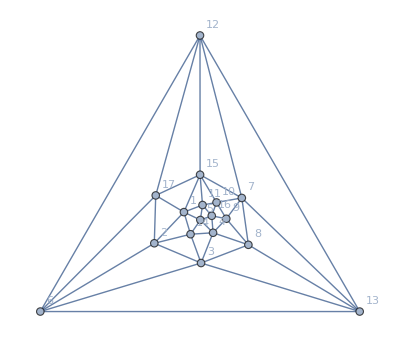

```mathematica
plantri8=Graph[{12<->13,12<->7,12<->15,12<->17,12<->6,13<->6,13<->3,13<->8,13<->7,7<->8,7<->9,7<->10,7<->15,15<->10,15<->11,15<->1,15<->17,17<->1,17<->2,17<->6,6<->2,6<->3,3<->2,3<->14,3<->4,3<->8,8<->4,8<->9,9<->4,9<->16,9<->10,10<->16,10<->11,11<->16,11<->5,11<->1,1<->5,1<->14,1<->2,2<->14,14<->5,14<->4,4<->5,4<->16,16<->5},GraphLayout->"TutteEmbedding",VertexLabels->"Name"]
```

```mathematica
FindPlantri[g_,from_,to_]:=Block[{i, found=-1},Monitor[For[i=from,i≤to,i++,
If[IsomorphicGraphQ[Graph[plantri[[i]]],g],found=i;Break[]]
],{from,i,to}
];
Return[found]
]
```

Read a plantri graph from a file generated by plantri

```mathematica
ReadPlantri[fileName_]:=Block[{file,vertices,result={},header,i, next,v, bigresult={}},
PrintTemporary["Reading " <> fileName];
file=OpenRead[fileName,BinaryFormat->True];
(* read header *)
For[i=1,i≤StringLength[">>planar_code<<"],i++,
header=BinaryRead[file];
];
vertices=BinaryRead[file];
Monitor[
While[vertices=!=EndOfFile,
result={};
For[v=1,v≤vertices,v++,
next=BinaryRead[file];
While[next ≠ 0,
result=Append[result,If[v<next,v<->next,next<->v]];
next=BinaryRead[file];
];
];
bigresult=Append[bigresult,Sort[DeleteDuplicates[result]]];
vertices=BinaryRead[file];
],
Length[bigresult]
];
Close[file];
PrintTemporary["Done. " <> ToString[Length[bigresult]]];
bigresult
]
```

### For a pro grpah, discover the pentagon vertices around the inner pentagon, given by the vertices and edges. The returned list is a set of edges in arbitrary order

```mathematica
DiscoverOuterPentagon[g_,innerVertices_, innerEdges_]:=Block[{result={},  inner=innerVertices,h=EdgeDelete[g,innerEdges],neighbours},
Table[
neighbours=DeleteDuplicates[Select[Flatten[Map[{#[[1]],#[[2]]}&,EdgeList[h,innerVertex<->_]]],#≠innerVertex&]];
result=Join[result,neighbours]
,{innerVertex, innerVertices}
];
DeleteDuplicates[result]
]
```

### Create a graph with an inner and an outer “pentagon”, ready for painting. We pick an arbitrary nodes with degree 5 to start from

```mathematica
DeleteHeartAndPaint[g_]:=Block[{vertices,innerVertices,center,h,innerEdges,outerVertices,outerEdges, completeOuter, completeOuterEdges},
vertices=Select[VertexList[g],VertexDegree[g,#]==5&];
center=First[vertices];
innerVertices=DeleteDuplicates[Select[Flatten[Map[{#[[1]],#[[2]]}&,EdgeList[g,center<->_]]],#≠center&]];
innerEdges=DiscoverCycle[g,innerVertices];
h=VertexDelete[g,center];
outerVertices=DiscoverOuterVertices[h,innerEdges];
outerEdges=DiscoverCycle[g,outerVertices];
completeOuter=DiscoverOuterPentagon[h,innerVertices,innerEdges];
completeOuterEdges=DiscoverCycle[g,completeOuter];
Graph[h,
EdgeStyle->Join[Map[#->{Thick,Red}&,innerEdges],Map[#->{Thick,Darker[Green]}&,completeOuterEdges]],
VertexShape->Map[#->Graphics[{EdgeForm[{Thick,Blue}],Yellow,Disk[{0,0},20]}]&,outerVertices],
GraphLayout->"TutteEmbedding",
VertexSize->Large,
VertexLabels->"Name",
ImageSize->400
]
]
```

## Compatibility matrix

The following code builds a matrix that compares the possible color combinations for each vertex pair (even those not connected) before and after an operation.  The result is formatted as a graph.

```mathematica
FindGraphInSet[g_,set_]:=Block[{result=-1},
For[k=1,k≤Length[set],k++,
If[IsomorphicGraphQ[g,set[[k]]],result=k;Break[]]
];
result
]
```

```mathematica
ColorsForEdgeOperationMatrix[g_,edges_,operation_]:=Block[{ sols,sols2,h, result,mat,mat2,bg,bigResult,one,two,three,first2,second2},
one=Graph[{1<->1,2<->2,3<->3,4<->4}];
two=CompleteGraph[4];
three=EdgeAdd[ two,EdgeList[one]];
PrintTemporary["Solving g.."];
sols=Solve[ToEquations[g],SymbolRange[g]];
PrintTemporary["Solved g"];
Monitor[
bigResult=Table[
PrintTemporary["Solving h.." <> ToString[e]];
h=operation[g,e];
sols2=Solve[ToEquations[h],SymbolRange[h]];
PrintTemporary["Solved h "  <> ToString[e]];
result=MatrixForm[
Table[
bg=None;
Framed[
With[
{first=If[
VertexQ[g,i]&&VertexQ[g,j],
Graph[DeleteDuplicates[Map[Sort[{Symbol["x"<>ToString[i]],Symbol["x"<>ToString[j]]}/.#]&,sols]],ImageSize->20, DirectedEdges->False],
"ϵ"],
second=If[
VertexQ[h,i]&&VertexQ[h,j],
Graph[DeleteDuplicates[Map[Sort[{Symbol["x"<>ToString[i]],Symbol["x"<>ToString[j]]}/.#]&,sols2]],ImageSize->20, DirectedEdges->False],
"ϵ"
]
},
If[EdgeQ[first,1<->1],bg=LightPurple];
If[EdgeQ[second,1<->1],bg=LightGreen];
If[EdgeQ[g,i<->j],bg=LightBlue;If[!EdgeQ[h,i<->j],bg=LightRed;]];
If[i==j,bg=LightYellow];
first2=FindGraphInSet[first,{one,two,three}];
If[first2==-1,first2=first];
second2=FindGraphInSet[second,{one,two,three}];
If[second2==-1,second2=second];
If[first2==second2,first2,
first2->second2
]
],
Background->bg
],
{i,VertexList[g]},
{j,VertexList[g]}],
TableHeadings->{VertexList[g], VertexList[g]},
TableSpacing->{0, 0}
];
Labeled[result,{operation,e}],
{e,edges}
],
{operation,e,i,j}
];
bigResult
]
```

```mathematica
ColorSubMatrix[sols_,e1_,e2_]:=Block[{subList,result},
subList=Map[{Symbol["x"<>ToString[e1]],Symbol["x"<>ToString[e2]]}/.#&,sols];
result=Table[With[{color1=i[[1]],color2=i[[2]]},
Length[Select[subList,#[[1]]==color1&&#[[2]]==color2&]]*i[[3]]
],
{i,{{1,1,1/6},{1,2,1/2}}}];
result
]
```

```mathematica
DoNothing[g_,e_]:=g
```

```mathematica
ColorMainMatrix[graph_,graphFormat_:FormatGraph,vertices_:Null]:=Block[{sols,result,bg, sorted},
PrintTemporary["Solving g.." ];
sorted=Graph[Sort[VertexList[graph]],Sort[EdgeList[graph],EdgeComp]];
sols=Solve[ToEquations[sorted],SymbolRange[sorted]];
PrintTemporary["Solved g" ];
result=TableForm[
Table[
bg=None;
If[i≤j,
Framed[
With[
{
mat=ColorSubMatrix[sols,i,j]
},

If[mat[[1]]==0,bg=LightRed];
If[MemberQ[vertices,i]&&MemberQ[vertices,j],bg=LightRed];
If[i==j,bg=LightYellow];
If[EdgeQ[sorted,i<->j],bg=LightBlue];
TableForm[mat]
],
Background->bg
],
""
],
{i,VertexList[sorted]},
{j,VertexList[sorted]}],
TableHeadings->{VertexList[sorted], VertexList[sorted]},
TableSpacing->{0, 0}
];
{graphFormat[sorted],result}
]
```

```mathematica
FormatGraph[g_]:=Graph[g,GraphLayout->"TutteEmbedding",VertexLabels->"Name",PlotLabel->ChromaticPolynomial[g,4],ImageSize->300]
```

```mathematica
ColorMatrixForEdgeOperationMatrix[g_,edges_,ops_,graphFormat_ : FormatGraph,vertices_ : Null]:=Block[{ sols2,h, result,bg,bigResult},
Monitor[
bigResult=Prepend[
Table[
h=op[g,e];
result=ColorMainMatrix[h,graphFormat,vertices];
Labeled[result,{op,e}],
{e,edges},
{op, ops}
],Labeled[ColorMainMatrix[g,graphFormat,vertices],"full"]
],
{op,e,i,j}
];
bigResult
]
```

```mathematica
ColorsForEdgeDeleteMatrix[g_,edges_]:=ColorsForEdgeOperationMatrix[g,edges,EdgeDelete]
```

```mathematica
ColorsForEdgeContractMatrix[g_,edges_]:=ColorsForEdgeOperationMatrix[g,edges,EdgeContract]
```

```mathematica
EdgeComp[x_,y_]:=Block[{a,b},
a=Sort[{x[[1]],x[[2]]}];
b=Sort[{y[[1]],y[[2]]}];
If[a[[1]]<b[[1]],
True,
a[[2]]<b[[2]]
]
]
```

## Generating all graphs etc ...

```mathematica
CircleLayout[n_]:=Table[{Cos[(2π/n )(n-i+1)+Pi/2],Sin[(2π/n )(i-1)+Pi/2]},{i,n}]
```

```mathematica
totalDone=0;
```

```mathematica
GenAll[n_]:=Block[
{nodes},
totalDone=0;
nodes=Table[{i},{i,n}];
GenAllFromList[nodes]
]
```

```mathematica
PairWiseCombine[list_]:=Block[
{l=Length[list], sets,result={},temp,newItem},
sets=Subsets[Range[l],{2}];
result=Table[
temp=Table[k,{k,list}];
newItem=Sort[{s[[1]],s[[2]]}];
temp=Drop[temp,{newItem[[2]]}];
temp=Drop[temp,{newItem[[1]]}];
temp=Append[temp,Sort[Join[list[[newItem[[1]]]],list[[newItem[[2]]]]]]];
temp=Sort[temp];
temp
,
{s,sets}
];
result
]
```

```mathematica
MyCircle2[vertices_,length_]:=Block[{pos=N[ CircleLayout[length]], midPoint,temp,i,div},
midPoint=Mean[Table[pos[[v]],{v,vertices}]];
div=Sqrt[midPoint[[1]]^2+midPoint[[2]]^2];
If[True,
midPoint=pos[[vertices[[1]]]],
midPoint=midPoint/div
];
N[midPoint]
]
```

```mathematica
MyCircle[vertices_,length_]:=Block[{pos=N[ CircleLayout[length]], sum={0,0}},
Map[MyCircle2[#,length]&,vertices]
]
```

```mathematica
AllGraphs[list_]:=Block[
{l=Length[list],longLength=Total[Map[Length[#]&,list]], sets,result={},temp,g, mat, element, realResult},
(* subsets are the vertices that we will connect *)
sets=Subsets[Subsets[Range[l],{2}]];
Monitor[
result=Table[
(* create a matrix that is "not connected" *)
mat=Table[0,{i,longLength},{j,longLength}];
(* Mark everything within one bucket as "2" *)
Table[
Table[mat[[i,j]]=2;mat[[j,i]]=2,{i,list[[bucket]]},{j,list[[bucket]]}],
{bucket,l}
];

(* Mark everything for linked edges as "1" *)
Table[
Table[mat[[i,j]]=1;mat[[j,i]]=1,{i,list[[s2[[1]]]]},{j,list[[s2[[2]]]]}],
{s2,s}
];
g=Graph[Range[l],
Table[
s2[[1]]<->s2[[2]]
,{s2,s}
],
VertexLabels->Table[i->StringRiffle[ list[[i]],","],{i,l}],
VertexCoordinates->MyCircle[list,longLength],
VertexStyle->Red,
VertexSize->0.1,
EdgeStyle->{Thickness[0.02],Darker[Green]},
ImageSize->{50,50}
];
totalDone++;
element=Association[];
element["signature"]=GraphMatrixSignature[mat];
element["matrix"]=mat;
element["graph"]=g;
element["vertexsets"]=list;
element["vertices"]=Range[l];
element["edges"]=s;
element["relations"]={};
element["links"]={};
element
,
{s,sets}
];
realResult=Association[];
Table[
realResult[el["signature"]]=el,
{el,result}
];
realResult,
totalDone
]
]
```

```mathematica
GenAllFromList[{{4},{6},{1,3},{2,5}}]//First
```

{{4},{6},{1,3},{2,5}}

```mathematica
GenAllFromList[list_]:=Block[
{nodes,result},

result=AllGraphs[list];
If[Length[list]>1,
Table[
Table[
result[el["signature"]]=el,
{el,GenAllFromList[v]}
]
,
{v,PairWiseCombine[list]}
]
];
result
]
```

```mathematica
GraphMatrixSignature[matrix_]:=Block[{l=Length[matrix]},
FromDigits[
Flatten[
Table[Table[matrix[[i,j]],{j,i+1,l}],{i,1,l}]
],3]
]
```

```mathematica
GraphMatrixSignature2[matrix_,indexSet1_,indexSet2_, newValue_]:=Block[
{temp=matrix, result},
Table[
temp[[i2,j2]]=newValue;
temp[[j2,i2]]=newValue;
,{i2,indexSet1},{j2,indexSet2}];

Table[
temp[[i,i]]=2;
,{i,Length[temp]}];
result=GraphMatrixSignature[temp];
Print["---->", result, temp];
result
]
```

```mathematica
CompressGraph[full_,vertices_]:=Block[
{x,y,l=Length[vertices],a,b},
Table[
a=vertices[[i,1]];
b=vertices[[j,1]];
full[[a,b]]
,{i,l},{j,l}
]
]
```

```mathematica
UnCompressGraph[small_,vertices_]:=Block[
{x,l=Total[Map[Length[#]&,vertices]],a,b,result,l2=Length[vertices]},
result=Table[0,{i,l},{j,l}];
Table[
a=vertices[[i]];
b=vertices[[j]];
x=small[[i,j]];
Table[
result[[a1,b1]]=x,{a1,a},{b1,b}
]
,{i,l2},{j,l2}
];
result
]
```

```mathematica
GraphMatrixSignature2[currentCompressed_,i_,j_,value_,currentVertexSets_]:=Block[
{uncomp=currentCompressed,sig,mat,l=Length[currentCompressed],m},
(* if the value is 2 then we run over the columns i and j and assign the maximum of both columns to each.
  This makes sure that connected stays connected and merged stays merged *)
If[value==2,
Table[
m=Max[uncomp[[i,a]],uncomp[[j,a]]];
uncomp[[j,a]]=m;
uncomp[[i,a]]=m;

uncomp[[a,j]]=m;
uncomp[[a,i]]=m
,{a,l}];

(*Print["uncomp",i, "  ", j, "  ",sig, "  ",MatrixForm[uncomp]];*)

];
uncomp[[i,j]]=value;
uncomp[[j,i]]=value;
mat=UnCompressGraph[uncomp,currentVertexSets];
sig=GraphMatrixSignature[mat];
(*Print["uncompressed",i, "  ", j, "  ",sig, "  ",MatrixForm[currentCompressed]-> MatrixForm[mat]];*)
sig
]
```

```mathematica
CompleteRelations[assocs_]:=Block[
{current, currentGraph, currentID,currentMatrix,currentVertexSets, currentCompressed,one,two, relations={}, links,l, newAssocs=Association[],keep, count=0},
Monitor[
Table[
count++;
current=assocs[key];
currentGraph=current["graph"];
currentID=current["signature"];
currentMatrix=current["matrix"];
currentVertexSets=current["vertexsets"];
currentCompressed=CompressGraph[currentMatrix,currentVertexSets];
keep=currentCompressed;
l=Length[currentCompressed];
links={};
relations={};

Table[
currentCompressed=keep;
If[currentCompressed[[i,j]]==2,
(* current is contracted of one and two *)
one=GraphMatrixSignature2[currentCompressed,i,j,1,currentVertexSets];
two=GraphMatrixSignature2[currentCompressed,i,j,0,currentVertexSets];


If[KeyExistsQ[assocs,two]&&KeyExistsQ[assocs,one],
AppendTo[relations,Symbol["x"<>ToString[key]]== Symbol["x"<>ToString[two]]-Symbol["x"<>ToString[one]]]
,
Print[one, "   ",KeyExistsQ[assocs,one],"  ", two, "   ",KeyExistsQ[assocs,two], "  ", currentMatrix//MatrixForm, "   ", keep//MatrixForm, "   ",i , "   ", j, "  3333 ", currentVertexSets];
Interrupt[]
]
,
If[currentCompressed[[i,j]]==1,
(* current is connected of one and two *)
one=GraphMatrixSignature2[currentCompressed,i,j,2,currentVertexSets];
two=GraphMatrixSignature2[currentCompressed,i,j,0,currentVertexSets];


If[KeyExistsQ[assocs,two]&&KeyExistsQ[assocs,one],
AppendTo[relations,Symbol["x"<>ToString[key]]== Symbol["x"<>ToString[two]]-Symbol["x"<>ToString[one]]]
,
Print[one, "   ",KeyExistsQ[assocs,one],"  ", two, "   ",KeyExistsQ[assocs,two], "  ", currentMatrix//MatrixForm, "   ", keep//MatrixForm, "   ",i , "   ", j, "  3333 ", currentVertexSets];
Interrupt[]
]
,
(* current is unconnected of one and two *)
one=GraphMatrixSignature2[currentCompressed,i,j,2,currentVertexSets];
two=GraphMatrixSignature2[currentCompressed,i,j,1,currentVertexSets];
AppendTo[links,one];
AppendTo[links,two];

If[KeyExistsQ[assocs,two]&&KeyExistsQ[assocs,one],
AppendTo[relations,Symbol["x"<>ToString[key]]== Symbol["x"<>ToString[two]]+Symbol["x"<>ToString[one]]]
,
Print[one, "   ",KeyExistsQ[assocs,one],"  ", two, "   ",KeyExistsQ[assocs,two], "  ", currentMatrix//MatrixForm, "   ", keep//MatrixForm, "   ",i , "   ", j, "  3333 ", currentVertexSets];
Interrupt[]
]
]
]
,{i,1,l},{j,i+1,l}
];
current["relations"]=relations;
(*PrintTemporary[relations];*)
current["links"]=links;
newAssocs[key]=current
,
{key, Sort[Keys[assocs]]}
],
{count,key}];
newAssocs
]
```

```mathematica
SymbolComp[x_,y_]:=Block[{a,b,o,p},
a=StringTake[SymbolName[x],1];
b=StringTake[SymbolName[y],1];
If[a≠b,Return[a<b]];
o=FromDigits[StringPadLeft[StringDrop[SymbolName[x],1],3,"0"]];
p=FromDigits[StringPadLeft[StringDrop[SymbolName[y],1],3,"0"]];
Return[o<p]
]
TrueQ["c">"b"]
False
ExpComp[d1>0,d10>0]
False
LongSymbol[x_]:=Block[{comp, start,end},
comp=ToString[x];
start=StringTake[comp,1];
end=StringPadLeft[ StringDrop[comp,1],3,"0"];
start<>end
]
ExpComp[x_,y_]:=Block[{
varx=getAllVariables[x],
vary=getAllVariables[y],
o,p},
If[Length[varx]≠Length[vary],
Return [Length[varx]<Length[vary]]
];
varx=Sort[varx,SymbolComp];
vary=Sort[vary,SymbolComp];
o=StringJoin[Map[ LongSymbol,varx]];
p=StringJoin[Map[LongSymbol,vary]];
Order[o,p]>0
]
ExpressionToTable2[exp_]:=Block[
{vals=Sort[Monitor[Table[exp[[i]]//Simplify,{i,1,Length[exp]}],{i,Length[exp]}]]},
TableForm[Sort[vals,ExpComp],TableDirections->Column]
]
```

False

False

ExpComp[d1>0,d10>0]

False

```mathematica
ExpressionToList[exp_]:=Table[exp[[k]],{k,Length[exp]}]
```

```mathematica
ExpressionToTable[exp_]:=Block[
{vals=Sort[Monitor[Table[exp[[i]]//Simplify,{i,1,Length[exp]}],{i,Length[exp]}]]},
TableForm[Sort[vals,ExpComp],TableDirections->Column]
]
```

```mathematica
OnlyOnex[exp_]:=Block[{
v=getAllVariables[exp]},
Length[Select[v,StringTake[ SymbolName[#],1]=="x"&]]==1
]
```

```mathematica
NotASingleX[exp_]:=Block[{
v=ListofVars[exp]//DeleteDuplicates},
Length[Select[v,StringTake[ SymbolName[#],1]=="x"&]]==0
]
```

```mathematica
OnlyTwox[exp_]:=Block[{
v=getAllVariables[exp]},
Length[Select[v,StringTake[ SymbolName[#],1]=="x"&]]==2
]
```

```mathematica
OnlyXVar[exp_]:=Block[{
v=getAllVariables[exp]},
First[Select[v,StringTake[ SymbolName[#],1]=="x"&]]
]
```

```mathematica
XVar[exp_]:=Block[{
v=getAllVariables[exp]},
Select[v,StringTake[ SymbolName[#],1]=="x"&]
]
```

```mathematica
GraphMatrixSignature[({{2,0,1,1},{0,2,0,0},{1,0,2,2},{1,0,2,2}})]
```

110

```mathematica
AllGraphs[{{1},{2},{3,4}}]//DeleteDuplicates
```

<|2→<|signature→2,matrix→{{2,0,0,0},{0,2,0,0},{0,0,2,2},{0,0,2,2}},graph→-Graphics-,vertexsets→{{1},{2},{3,4}},vertices→{1,2,3},edges→{},relations→{},links→{}|>,245→<|signature→245,matrix→{{2,1,0,0},{1,2,0,0},{0,0,2,2},{0,0,2,2}},graph→-Graphics-,vertexsets→{{1},{2},{3,4}},vertices→{1,2,3},edges→{{1,2}},relations→{},links→{}|>,110→<|signature→110,matrix→{{2,0,1,1},{0,2,0,0},{1,0,2,2},{1,0,2,2}},graph→-Graphics-,vertexsets→{{1},{2},{3,4}},vertices→{1,2,3},edges→{{1,3}},relations→{},links→{}|>,14→<|signature→14,matrix→{{2,0,0,0},{0,2,1,1},{0,1,2,2},{0,1,2,2}},graph→-Graphics-,vertexsets→{{1},{2},{3,4}},vertices→{1,2,3},edges→{{2,3}},relations→{},links→{}|>,353→<|signature→353,matrix→{{2,1,1,1},{1,2,0,0},{1,0,2,2},{1,0,2,2}},graph→-Graphics-,vertexsets→{{1},{2},{3,4}},vertices→{1,2,3},edges→{{1,2},{1,3}},relations→{},links→{}|>,257→<|signature→257,matrix→{{2,1,0,0},{1,2,1,1},{0,1,2,2},{0,1,2,2}},graph→-Graphics-,vertexsets→{{1},{2},{3,4}},vertices→{1,2,3},edges→{{1,2},{2,3}},relations→{},links→{}|>,122→<|signature→122,matrix→{{2,0,1,1},{0,2,1,1},{1,1,2,2},{1,1,2,2}},graph→-Graphics-,vertexsets→{{1},{2},{3,4}},vertices→{1,2,3},edges→{{1,3},{2,3}},relations→{},links→{}|>,365→<|signature→365,matrix→{{2,1,1,1},{1,2,1,1},{1,1,2,2},{1,1,2,2}},graph→-Graphics-,vertexsets→{{1},{2},{3,4}},vertices→{1,2,3},edges→{{1,2},{1,3},{2,3}},relations→{},links→{}|>|>

```mathematica
headlist={Or,And,Equal,Unequal,Less,LessEqual,Greater,GreaterEqual,Inequality};

getAllVariables[f_?NumericQ]:=Sequence[]
getAllVariables[{}]:=Sequence[]
getAllVariables[t_]/;MemberQ[headlist,t]:=Sequence[]

getAllVariables[ll_List]:=Flatten[Union[Map[getAllVariables[#]&,ll]]]

getAllVariables[Derivative[n_Integer][f_][arg__]]:=getAllVariables[{arg}]

getAllVariables[f_Symbol[arg__]]:=Module[{fvars},If[MemberQ[Attributes[f],NumericFunction]||MemberQ[headlist,f],fvars=getAllVariables[{arg}],(*else*)fvars=f[arg]];
fvars]

getAllVariables[other_]:=other
```

```mathematica
ListofVars[exp_]:=With[{kk=getAllVariables[exp]},If[TrueQ[kk==BlankNullSequence[]],{kk},If[ListQ[kk],kk,{kk}]]]
```

```mathematica
CosyPrint[key_]:=With[
{current=newAssoc[key]},
Framed[Labeled[Row[{
Graph[current["graph"],ImageSize->{50,50}],"   ",
Graph[VertexList[current["graph"]],EdgeList[current["graph"]],GraphLayout->"TutteEmbedding",ImageSize->{50,50}],"   ",
Style[TableForm[Map[FullSimplify[#/.replaceMents/.α+β+γ+δ+ϵ-λ->α1+β1+γ1+δ1+ϵ1]&,
current["relations"]]],FontSize->12, FontFamily->"Consolas"], "   ",
MatrixForm[current["matrix"]]
}
],Style[
{If[KeyExistsQ[current,"colofour"],
current["signature"]->TraditionalForm[current["colofour"]/.replaceMents/.α+β+γ+δ+ϵ-λ->α1+β1+γ1+δ1+ϵ1],
current["signature"]
],ChromaticPolynomial[current["graph"],4]/24},Red]]]
]
```

```mathematica
CosyPrint2[key_]:=With[
{current=newAssoc[key]},
Framed[Labeled[Row[{
Graph[current["graph"],ImageSize->{50,50}],"   ",
Graph[VertexList[current["graph"]],EdgeList[current["graph"]],GraphLayout->"TutteEmbedding",ImageSize->{50,50}],"   ",
Style[TableForm[Map[FullSimplify[#]&,
current["relations"]]],FontSize->12, FontFamily->"Consolas"], "   ",
MatrixForm[current["matrix"]]
}
],Style[
{current["signature"]->
If[KeyExistsQ[current,"comp"],current["comp"],GreaterEqual][TraditionalForm[current["colofour"]/.replaceMents/.α+β+γ+δ+ϵ-λ->α1+β1+γ1+δ1+ϵ1]
,0],If[KeyExistsQ[current,"compwhy"],current["compwhy"],""]},Red]]]
]
```

```mathematica
SymbolComp2[x_,y_]:=Block[{n1=SymbolName[x],n2=SymbolName[y],a,b,h1,h2},
h1=StringTake[n1,1];
h2=StringTake[n2,1];
If[h1≠h2,
Return[h1<h2]
];
a=SymbolToKey[n1];
b=SymbolToKey[n2];
a<b
]
```

```mathematica
CoeffVector[v_]:=Table[Coefficient[ (v/.replaceMents)*24,v,1],{v,Sort[myVars,SymbolComp2]}]
```

```mathematica
CosyPrint3[key_]:=With[
{current=newAssoc[key]},
Column[
{
Framed[Labeled[Row[{
Graph[current["graph"],ImageSize->{50,50}],"   ",
Graph[VertexList[current["graph"]],EdgeList[current["graph"]],GraphLayout->"TutteEmbedding",ImageSize->{50,50}],"   ",
Style[MatrixForm[Map[First,current["colortable3"]],TableHeadings->{Map[#[[1]]<->#[[2]]&,Subsets[Range[5],{2}]], "="}, TableSpacing->{2, 3}],FontSize->10, FontFamily->"Consolas"]
}
],Style[
{current["signature"]->
If[KeyExistsQ[current,"comp"],current["comp"],GreaterEqual][TraditionalForm[current["colofour"]]
,0],If[KeyExistsQ[current,"compwhy"],current["compwhy"],""]},Red]]],
Style[MatrixForm[Map[Last,current["colortable3"]],TableHeadings->{Map[#[[1]]<->#[[2]]&,Subsets[Range[5],{2}]], {"≠"}}, TableSpacing->{2, 3}],FontSize->10, FontFamily->"Consolas"]
}
]
]
```

```mathematica
CosyPrint4[key_]:=With[
{current=newAssoc[key]},
Framed[Labeled[Row[{
Graph[current["graph"],ImageSize->{50,50}],"   ",
Graph[VertexList[current["graph"]],EdgeList[current["graph"]],GraphLayout->"TutteEmbedding",ImageSize->{50,50}],"   ",
Style[MatrixForm[Map[First,current["colortable3"]],TableHeadings->{Map[#[[1]]<->#[[2]]&,Subsets[Range[5],{2}]], "="}, TableSpacing->{2, 3}],FontSize->10, FontFamily->"Consolas"],
Style[MatrixForm[Map[Last,current["colortable3"]],TableHeadings->{Map[#[[1]]<->#[[2]]&,Subsets[Range[5],{2}]], {"≠"}}, TableSpacing->{2, 3}],FontSize->10, FontFamily->"Consolas"]
}
],Style[
{current["signature"]->
If[KeyExistsQ[current,"comp"],current["comp"],GreaterEqual][TraditionalForm[current["colofour"]]
,0],If[KeyExistsQ[current,"compwhy"],current["compwhy"],""]},Red]]]
]
```

```mathematica
ComposeInEq[key_]:=Block[{current=newAssoc[key],op, table,result,colofour},
table=current["colortable3"];
op=current["comp"];
colofour=current["colofour"];
DeleteDuplicates[
Flatten[
Table[
result=Join[
Table[With[{eq=table[[k,1]],noteq=table[[k,2]]},
If[NumberQ[eq]||NumberQ[noteq],
True,
{(op[eq,0]||op[noteq,0]),(eq≥0),(noteq≥0)}
]
],{k,1,10}]
,{op[colofour,0]}];
result
,
{comp,Subsets[Range[5],{2}]}]
]
]
]
```

```mathematica
ComposeInEq2[key_, hardFacts_]:=Block[{current=newAssoc[key],op, table,result,colofour},
table=current["colortable3"];
op=current["comp"];
colofour=current["colofour"];
DeleteDuplicates[
Flatten[
Table[
result=Join[
Table[With[{eq=table[[k,1]],noteq=table[[k,2]]},
If[NumberQ[eq]||NumberQ[noteq],
True,
{(Simplify[op[eq,0]||op[noteq,0]&& hardFacts]),(eq≥0),(noteq≥0)}
]
],{k,1,10}]
,{op[colofour,0]}];
result
,
{comp,Subsets[Range[5],{2}]}]
]
]
]
```

```mathematica
ComposeHardFacts[]:=Block[{},
Simplify[
Fold[And,
Table[newAssoc[key]["comp"][newAssoc[key]["colofour"],0],{key,Keys[newAssoc]}]
]
]
]
```

```mathematica
Length[newAssoc[1]["colortable3"][[1]]]
```

0

```mathematica
EmbedGraph[key_]:=Block[{val=newAssoc[key], sets, reference={2,6,5,4,3}, g, sub},
sets=val["vertexsets"];
g=VertexDelete[ Graph[plantri[[10000]]],1];
g=EdgeDelete[ g,{2<->6,6<->5,5<->4,4<->3,3<->2}];
Table[If[Length[s]>1,
g=VertexContract[g,Table[reference[[v]],{v,s}]]
], {s,sets}];
sub=val["graph"];
Table[
g=EdgeAdd[g,{reference[[First[sets[[e[[1]]]]]]]<->reference[[First[sets[[e[[2]]]]]]]}],{e,EdgeList[sub]}];

g
]
```

```mathematica
(*newAssoc=Get["d:\\newAssoc4-4.m"];Length[newAssoc]*)
```

```mathematica
graphics=Table[key->newAssoc[key]["graph"],{key,Keys[newAssoc]}];
```

Keys::invrl: The argument newAssoc is not a valid Association or a list of rules.

Table::iterb: Iterator {key,Keys[newAssoc]} does not have appropriate bounds.

```mathematica
graphassoc=Association[];
Table[graphassoc[key]=newAssoc[key]["graph"],{key,Keys[newAssoc]}];
```

Keys::invrl: The argument newAssoc is not a valid Association or a list of rules.

Table::iterb: Iterator {key,Keys[newAssoc]} does not have appropriate bounds.

```mathematica
Length[graphassoc]
```

0

```mathematica
alfaKey=35977;
betaKey=31681;
gammaKey=23041 ;
deltaKey=20803;
epsilonKey=27259;
alfa1Key=36166;
beta1Key=31738;
gamma1Key=29608;
delta1Key=36112;
epsilon1Key=31714;
lambdaKey=20665;
starKey=8859;k5Key=29524;
```

```mathematica
star6Key=5039860;
```

```mathematica
alfa1s={alfa1Key,beta1Key,gamma1Key,delta1Key,epsilon1Key};
```

```mathematica
amigo1=29413;amigo2=20773;amigo3=27229;amigo4=22933;amigo5=20695;
```

```mathematica
amigos={amigo1,amigo2,amigo3,amigo4,amigo5};
```

```mathematica
alfas={alfaKey,betaKey,gammaKey,deltaKey,epsilonKey};
```

```mathematica
quad1Key=36085;
quad2Key=29605;
quad3Key=29527;
quad4Key=31711;
quad5Key=29551;
```

```mathematica
quads={quad1Key,quad2Key,quad3Key,quad4Key,quad5Key};
```

```mathematica
SymbolToKey[s_]:=Block[{tail=StringDrop[SymbolName[s],1], temp},
temp=ToExpression[tail];
If[!NumericQ[temp],
tail,
temp]
]
```

```mathematica
ColorTablePrint[key_,assoc_,colofour_,colortable_,rep_:{},cellsize_:200]:=Block[{current,equals,cellformat, headingFormat,nodeCount},
cellformat=TextCell[Style[#,10],CellFrame->{{0,0},{0,.5}},CellFrameColor->Darker[Green],CellSize->{cellsize,Automatic}, TextAlignment->Center]&;
headingFormat=Style[#,Red,FontSize->11,FontFamily->"Tahoma"]&;
current=assoc[key];
nodeCount=Length[Flatten[current["vertexsets"]]];
Column[
{
Labeled[Graph[current["graph"],ImageSize->{60,60},EdgeStyle->Blue],{headingFormat[key],headingFormat[assoc[key][colofour]/.rep],With[{t=ToString[assoc[key]["comp"]]},If[t=="Greater",Style[t,Darker[Green]],Style[t,10,Red]]]},{Left,Right,Top}],
Style[MatrixForm[Map[Map[cellformat[#]&,#]&,current[colortable]],TableHeadings->{Map[headingFormat[#[[1]]<->#[[2]]]&,Subsets[Range[nodeCount],{2}]],Map[ headingFormat,{"=","≠"}]}, TableSpacing->{0, 0}],FontSize->12, FontFamily->"Tahoma"]/.rep
},
Alignment->Center
]
]
```

## Partitions and key generation

```mathematica
KeyToSymbol[key_]:=Symbol["x"<>ToString[key]]
```

```mathematica
SetToString[set_]:=StringRiffle[Table[ToString[k],{k,Sort[set]}],""]
```

```mathematica
PartitionToSymbol[part_,prefix_:"v"]:=Block[{end},
end=StringRiffle[Map[SetToString[#]&,Sort[part,Min[#1]<Min[#2]&]],"x"];
Symbol[prefix<>end]]
```

```mathematica
IsPartitionGraph[g_,part_]:=Block[{needed=0,result=True},
If[VertexCount[g]≠Length[Flatten[part]],result=False];
Table[
Table[
needed++;
If[!EdgeQ[g,edge[[1]]<->edge[[2]]],result=False];
,
{edge,Subsets[set,{2}]}]
,{set,part}];
If[needed!=EdgeCount[g],result=False];
result
]
```

```mathematica
KSetPartitions[{}, 0] := {{}}
KSetPartitions[s_List, 0] := {}
KSetPartitions[s_List, k_Integer] := {} /; (k > Length[s])
KSetPartitions[s_List, k_Integer] := {Map[{#} &, s]} /; (k === Length[s])
KSetPartitions[s_List, k_Integer] :=
       Block[{$RecursionLimit = Infinity,j},
             Join[Map[Prepend[#, {First[s]}] &, KSetPartitions[Rest[s], k - 1]],
                  Flatten[
                     Map[Table[Prepend[Delete[#, j], Prepend[#[[j]], s[[1]]]],
                              {j, Length[#]}
                         ]&, 
                         KSetPartitions[Rest[s], k]
                     ], 1
                  ]
             ]
       ] /; (k > 0) && (k < Length[s])
KSetPartitions[0, 0] := {{}}
KSetPartitions[0, k_Integer?Positive] := {}
KSetPartitions[n_Integer?Positive, 0] := {}
KSetPartitions[n_Integer?Positive, k_Integer?Positive] := KSetPartitions[Range[n], k]
```

```mathematica
SetPartitions[{}] := {{}}
SetPartitions[s_List] := Flatten[Table[KSetPartitions[s, i], {i, Length[s]}], 1]
SetPartitions[0] := {{}}
SetPartitions[n_Integer?Positive] := SetPartitions[Range[n]]
```

```mathematica
GenerateAxioms[assoc_, vertexCount_]:=Block[
{keysWith6Nodes=Select[Keys[assoc],With[{g=assoc[#]["graph"]},VertexCount[g]==vertexCount]&],
allPartitions=SetPartitions[vertexCount]},
Monitor[ 
Table[
KeyToSymbol[ First[Select[keysWith6Nodes,With[{g=assoc[#]["graph"]},IsPartitionGraph[g,part]]&]]]->PartitionToSymbol[part],
{part,allPartitions}],part]
]
```

## Embedding graphs

```mathematica
EmbedGraph5[assoc_,key_]:=Block[{val=assoc[key], sets, reference={2,6,5,4,3}, g, sub},
sets=val["vertexsets"];
g=VertexDelete[ Graph[plantri[[10000]]],1];
g=EdgeDelete[ g,{2<->6,6<->5,5<->4,4<->3,3<->2}];
Table[If[Length[s]>1,
g=VertexContract[g,Table[reference[[v]],{v,s}]]
], {s,sets}];
sub=val["graph"];
Table[
g=EdgeAdd[g,{reference[[First[sets[[e[[1]]]]]]]<->reference[[First[sets[[e[[2]]]]]]]}],{e,EdgeList[sub]}];

g
]
```

```mathematica
EmbedGraph4[assoc_,key_]:=Block[{val=assoc[key], sets, reference={2,6,5,4}, g, sub},
sets=val["vertexsets"];
g=VertexDelete[ Graph[plantri[[10000]]],1];
g=EdgeDelete[ g,{2<->6,6<->5,5<->4,4<->3}];
Table[If[Length[s]>1,
g=VertexContract[g,Table[reference[[v]],{v,s}]]
], {s,sets}];
sub=val["graph"];
Table[
g=EdgeAdd[g,{reference[[First[sets[[e[[1]]]]]]]<->reference[[First[sets[[e[[2]]]]]]]}],{e,EdgeList[sub]}];

g
]
```

```mathematica
EmbedGraph6[assoc_,key_]:=Block[{val=assoc[key], sets, reference={1,2,10,11,12,4}, g, sub},
sets=val["vertexsets"];
g=VertexDelete[ Graph[plantri[[10000]]],3];
g=EdgeDelete[ g,{1<-> 2,2<->10,10<-> 11,11<->12,12<->4,4<->1}];
Table[If[Length[s]>1,
g=VertexContract[g,Table[reference[[v]],{v,s}]]
], {s,sets}];
sub=val["graph"];
Table[
g=EdgeAdd[g,{reference[[First[sets[[e[[1]]]]]]]<->reference[[First[sets[[e[[2]]]]]]]}],{e,EdgeList[sub]}];

g
]
```

```mathematica
EmbedGraph3[assoc_,key_]:=assoc[key,"graph"]
```

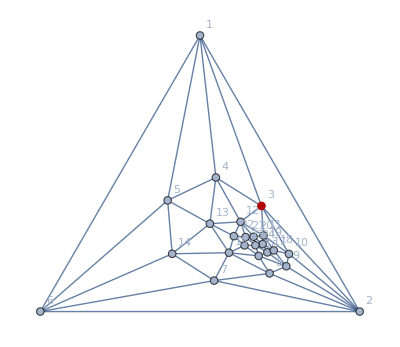

```mathematica
Graph[plantri[[10000]],VertexLabels->"Name",GraphLayout->"TutteEmbedding",GraphHighlight->{3}]
```

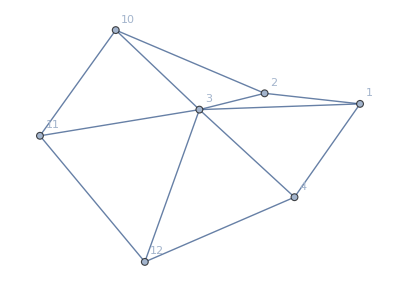

```mathematica
With[
{g=Graph[plantri[[10000]]]},
Graph[NeighborhoodGraph[g,3],VertexLabels->"Name"]
]
```

```mathematica
With[
{g=Graph[plantri[[10000]]]},
Table[{v->{VertexDegree[g,v],VertexList[NeighborhoodGraph[g,v]]}},{v,VertexList[g]}]
]
```

{{1→{5,{1,2,3,4,5,6}}},{2→{7,{2,1,3,6,7,8,9,10}}},{3→{6,{3,1,2,4,10,11,12}}},{4→{5,{4,1,3,5,12,13}}},{5→{5,{5,1,4,6,13,14}}},{6→{5,{6,1,2,5,7,14}}},{7→{5,{7,2,6,8,14,15}}},{8→{5,{8,2,7,9,15,16}}},{9→{6,{9,2,8,10,16,17,18}}},{10→{5,{10,2,3,9,11,18}}},{11→{6,{11,3,10,12,18,19,20}}},{12→{7,{12,3,4,11,13,20,21,22}}},{13→{6,{13,4,5,12,14,15,22}}},{14→{5,{14,5,6,7,13,15}}},{15→{7,{15,7,8,13,14,16,22,23}}},{16→{6,{16,8,9,15,17,23,24}}},{17→{5,{17,9,16,18,19,24}}},{18→{5,{18,9,10,11,17,19}}},{19→{5,{19,11,17,18,20,24}}},{20→{5,{20,11,12,19,21,24}}},{21→{5,{21,12,20,22,23,24}}},{22→{5,{22,12,13,15,21,23}}},{23→{5,{23,15,16,21,22,24}}},{24→{6,{24,16,17,19,20,21,23}}}}

## Planarity criterium

make a criterium for variables x and y to lie on the point between p1 and p2

```mathematica
MakeLineSegmentCrit[p1_,p2_, what_, x_, y_]:=Block[{result=True,diffx,diffy, back=Association[]},
If[p1[[1]]<p2[[1]],
result=p1[[1]]<x<p2[[1]],
If[p1[[1]]>p2[[1]],
result=p2[[1]]<x<p1[[1]],
result=x==p1[[1]]
]
];
If[p1[[2]]<p2[[2]],
result=result&&p1[[2]]<y<p2[[2]],
If[p1[[2]]>p2[[2]],
result=result&&p2[[2]]<y<p1[[2]],
result=result&&y==p1[[2]]
]
];
diffx=p2[[1]]-p1[[1]];
If[diffx≠0,
diffy=p2[[2]]-p1[[2]];
result=result&&((y-p1[[2]])==(diffy/diffx)*(x-p1[[1]]))
,
result=result&&(x==p1[[1]])
];
back["crit"]=result;
back["what"]=what;
back
]
```

The following piece of code sees whether a given graph is planar.  To do so, it creates tow sets of line segments.  The first are the edges of the graph.  The second is a line form each vertex to the position where the uncontrcated vertex was (but on a circle more outward).  None of the endpoints is part of the segment.  Then we look at intersections to see if the graph is planar

```mathematica
MyPlanar[assoc_,key_]:=Block[
{item=assoc[key], emb, pos=Association[],posOuter=Association[], length,lines={},sets,res,line1,line2,crit, found=False,mat,i,j,x,y, challenge},
x=Symbol["abcx"<>ToString[key]];
y=Symbol["abcy"<>ToString[key]];
emb=GraphEmbedding[item["graph"]];
length=Length[Flatten[item["vertexsets"]]];
mat=item["matrix"];
i=1;
Table[
Table[
pos[v]=IntegerPart[100*Round[emb[[i]],0.01]];
,{v,set}
];
i++
,{set,item["vertexsets"]}
];
Table[posOuter[k]=200*{Cos[(2π/length )(length-k+1)+Pi/2],Sin[(2π/length )(k-1)+Pi/2]},{k,length}];
Table[crit=MakeLineSegmentCrit[pos[k],posOuter[k], "Node is outward connected " <> ToString[k],x,y];lines=Append[ lines,crit],{k,length}];

Table[
i=Min[item["vertexsets"][[e[[1]]]]];
j=Min[item["vertexsets"][[e[[2]]]]];
crit=MakeLineSegmentCrit[pos[i],pos[j], "Connection between node " <> ToString[i<->j],x,y ];lines=Append[ lines,crit],
{e,EdgeList[item["graph"]]}
];

(*PrintTemporary["line segments computed : " ,Length[lines]];*)
sets=Subsets[Range[Length[lines]],{2}];
Table[
line1=lines[[s[[1]]]];
line2=lines[[s[[2]]]];
Quiet[
challenge=line1["crit"]&&line2["crit"];
res=NSolve[line1["crit"]&&line2["crit"],{x,y}];
];
If[res≠{},(*Print[key ,": Not planar because of ",s,stubbornForm6[key,"graph"], line1["what"],"  ",line1["crit"], "    ", line2["what"],"   ",  line2["crit"],  "     ", res];*)found=True;Return[True]];
,{s,sets}
];
!found
]
```

## Colours

```mathematica
ColourForKey[assoc_,key_]:=Block[{comp=Greater,atleast=0, result=Orange},
If[KeyExistsQ[assoc[key],"comp"],comp=assoc[key,"comp"]];
If[KeyExistsQ[assoc[key],"atleast"],atleast=assoc[key,"atleast"]];

If[comp===Greater || atleast >0,result=Darker[Green]];
If[comp ===Equal,result=Darker[Red]];
result
]
```

```mathematica
AndToTable[and_]:=Table[and[[k]],{k,Length[and]}]
```

```mathematica
InverseKey[assoc_,colofour_]:=First[Select[Keys[assoc],assoc["colofour"]==colofour&]]
```

## Generating graphs directly

```mathematica
VertexSetsFromMatrix[mat_]:=Block[{
result = {}, (* Will contain the vertext sets, a set of sets.  These are order so that 1 comes before 2 etc.*)
bucket = {}, (* Contains the current set of vertices that will go into result later *)
todo=Range[Length[mat]], (* contains vertices that have not yet been put in a bucket *)
row, (* current row in the matrix, also current vertex number *)
col (* current column in the matrix *)
},
For[row=1, row≤Length[mat], row++,
(* only process row if it has not yet been put in a bucket *)
If[MemberQ[todo,row],
(* now collect all columns that are marked with '2' and put them in the bucket *)
bucket={};
For[col=1, col ≤ Length[mat], col++,
If[MemberQ[todo,col],
If[mat[[row,col]]==2,
bucket = Append[bucket,col];
todo = Select[todo,#≠col&];
]
]
];
result = Append[result,bucket]
]
];
result
]
```

```mathematica
GraphFromMatrix[mat_,vertexSets_]:=Block[{
edges={},
vertices={},
vertexLabels={},
bucket = {}, (* Contains the current set of vertices that will go into result later *)
todo=Range[Length[mat]], (* contains vertices that have not yet been put in a bucket *)
row, (* current row in the matrix, also current vertex number *)
col, (* current column in the matrix *)
vertexToVertex=Association[],
newVertexToVertex=Association[],
currentVertex=0,
countNodes=Length[mat],
myvertexSets=vertexSets
},
If[myvertexSets==Null,myvertexSets=VertexSetsFromMatrix[mat]];
For[row=1, row≤Length[mat], row++,
(* only process row if it has not yet been put in a bucket *)
If[MemberQ[todo,row],
currentVertex++;
(* now collect all columns that are marked with '2' and put them in the bucket *)
bucket={};
For[col=1, col ≤ Length[mat], col++,
If[MemberQ[todo,col],
If[mat[[row,col]]==2,
bucket = Append[bucket,col];
vertexToVertex[col]=currentVertex;
todo = Select[todo,#≠col&]
]
]
];
newVertexToVertex[currentVertex]=bucket
]
];

(* now compute the edges *)
For[row=1, row≤Length[mat], row++,
For[col=row+1, col ≤ Length[mat], col++,
If[mat[[row,col]]==1,
edges=Append[edges,Sort[{vertexToVertex[row],vertexToVertex[col]}]]
]
]
];
edges=DeleteDuplicates[edges];
Graph[
Keys[newVertexToVertex],
edges,
VertexLabels->Table[i->StringRiffle[ newVertexToVertex[i],","],{i,Length[Keys[newVertexToVertex]]}],
VertexStyle->Red,
VertexSize->0.1,
VertexCoordinates->MyCircle[myvertexSets,countNodes],
EdgeStyle->{Thickness[0.02],Darker[Darker[Green]]},
ImageSize->{50,50}
]
]
```

```mathematica
MatrixFromGraph[g_]:=Block[{vertices=VertexList[g],mat,length=VertexCount[g]},
mat=Table[
Table[
If[row==col,2,If[EdgeQ[g,row<->col],1,0]]
,{col,length}
]
,{row,length}
]
]
```

```mathematica
allGraphs=Association[];
```

```mathematica
ComputeComp[assoc_,key_]:=Block[{current,g, clique},
current = assoc[key];
g=current["graph"];
current["comp"]=GreaterEqual;
current["compwhy"] = "No IH";
If[MyPlanar[assoc,key],
current["comp"]=Greater;
current["compwhy"] = "This is a planar contraction"
,
(* not planar contraction - look for K5 *)
clique=First[FindClique[g]];
If[Length[clique]≥5,
current["comp"]=Equal;
current["compwhy"] = "This graph contains Clique of size"<> ToString[Length[clique]]
]
];
current
]
```

## Compute color table

the following procedure only works if the vertexset represents a complete graph.

```mathematica
ComputeColorTable[vertexSets_]:=Block[
{vertexCount=Length[Flatten[vertexSets]], combinations, vertexToBucketNumber=Association[],left,right,colofour},

Table[Table[vertexToBucketNumber[v]=k,{v,vertexSets[[k]]}],{k,Length[vertexSets]}];
combinations=Subsets[Range[vertexCount],{2}];
colofour=PartitionToSymbol[vertexSets];
Table[
left=vertexToBucketNumber[c[[1]]];
right=vertexToBucketNumber[c[[2]]];

If[left==right,
{colofour,0},
{0,colofour}
]
,{c,combinations}
]
]
```

```mathematica
globalDepth=1
```

1

```mathematica
ComputeGraph[mat_,depth_]:=Block[{result,row,col,g, matJoin,matContract, rowBucket, colBucket,i,j, vertexSets,current,key,leftKey,rightKey, left, right,vertexSetLength,compressed, fromVertexToVertexSet,size,max,max2},
If[depth≤0,Interrupt[]];
(* first see if we can find it *)
globalDepth=depth;
key=GraphMatrixSignature[mat];

If[KeyExistsQ[allGraphs,key],
current = allGraphs[key];
result=key;
Return[key]
,
(* cannot find it : create an entry *)
vertexSets = VertexSetsFromMatrix[mat];
g=GraphFromMatrix[mat,vertexSets];
current=Association[];
current["signature"]=GraphMatrixSignature[mat];
current["matrix"]=mat;
current["graph"]=g;
current["vertexsets"]=vertexSets;
current["vertices"]=VertexList[g];
current["edges"]=EdgeList[g];
current["relations"]={};
current["links"]={};
current["parents"]={};
current["children"]={};
allGraphs[key]=current;
current=ComputeComp[allGraphs,key];
];

(*If[ToString[current["comp"]]=="Equal",
(* no need to go deeper iw we already have K5 *)
result=key;
current["colofour"]=0;
allGraphs[key]=current;
Return[key]
];*)
g=current["graph"];
vertexSets = current["vertexsets"];
vertexSetLength=Length[vertexSets];
size=Length[Flatten[vertexSets]];

(* see if it is a complete graph *)
If[CompleteGraphQ[g],
(* complete graph - try set comp and compwhy, colofour and colortable*)
result=key;
current["colofour"]=PartitionToSymbol[vertexSets];
current["colortable"]=ComputeColorTable[vertexSets];
,
(*  not a complete graph *)
For[row=1, row≤Length[mat], row++,
For[col=row+1, col ≤ Length[mat], col++,
(*for every vertex couple thatis not connected we compute the connected and the contracted form *)
If[mat[[row,col]]==0,
matJoin=mat;
matContract=mat;

(* first compute to which vertex set row and column belong*)
fromVertexToVertexSet=Association[];
Table[Table[fromVertexToVertexSet[v]=k,{v,vertexSets[[k]]}],{k,Length[vertexSets]}];
rowBucket=vertexSets[[fromVertexToVertexSet[row]]];
colBucket=vertexSets[[fromVertexToVertexSet[col]]];

(* now set the entries in contract and joined *)
Table[
matContract[[r,c]]=2;
matContract[[c,r]]=2;
matJoin[[r,c]]=1;
matJoin[[c,r]]=1
,
{r,rowBucket},
{c,colBucket}
];
(* now make sure the entries are consistent.  We take the max of the other entries *)
Table[
max=Max[Table[matContract[[r,v]],{r, rowBucket}]];
max2=Max[Table[matContract[[r,v]],{r, colBucket}]];
max=Max[max,max2];
Table[matContract[[r,v]]=max;matContract[[v,r]]=max,{r, rowBucket}];
Table[matContract[[r,v]]=max;matContract[[v,r]]=max,{r, colBucket}];
,
{v,size}
];

(* compute left and right *)
leftKey=ComputeGraph[matJoin,depth-1];
rightKey = ComputeGraph[matContract,depth-1];
left=allGraphs[leftKey];
right=allGraphs[rightKey];

(* if my position is not clear yet, try to see if the children can help *)
If[ToString[current["comp"]]=="GreaterEqual",
If[ToString[left["comp"]]=="Greater"||ToString[right["comp"]]=="Greater",
current["comp"]=Greater;
current["compwhy"]="The relation holds x"<> ToString[key]<> "== x"<> ToString[leftKey]<>"("<>ToString[left["comp"]]<> ") + "<> ToString[rightKey]<> 
" (" <>ToString[right["comp"]]<>")"
]
];

current["colofour"]=left["colofour"]+right["colofour"];
current["colortable"]=left["colortable"]+right["colortable"];
current["relations"]=Append[current["relations"],Symbol["x"<>ToString[key]]==Symbol["x"<>ToString[leftKey]]+Symbol["x"<>ToString[rightKey]]];
left["relations"]=Append[left["relations"],Symbol["x"<>ToString[leftKey]]==Symbol["x"<>ToString[key]]-Symbol["x"<>ToString[rightKey]]];
right["relations"]=Append[right["relations"],Symbol["x"<>ToString[rightKey]]==Symbol["x"<>ToString[key]]-Symbol["x"<>ToString[leftKey]]];

current["children"]=Append[current["children"],{leftKey,rightKey}];
left["parents"]=Append[left["parents"],key];
right["parents"]=Append[right["parents"],key];

allGraphs[leftKey]=left;
allGraphs[rightKey]=right;
result=key;

(* force a premature stop *)
(*col=size+1;
row=col;*)
]
]
]
];
allGraphs[key]=current;
result
]
```

```mathematica
ColourForRelation[assoc_,father_,childcouple_]:=Block[{
compFather=ToString[assoc[father,"comp"]],
left=ToString[assoc[childcouple[[1]],"comp"]],
right=ToString[assoc[childcouple[[2]],"comp"]]
},
If[compFather=="Greater",
If[left=="Greater" && right == "Equal",
Return[Green]
];
If[right=="Greater" && left == "Equal",
Return[Green]
];
If[left≠"Greater" && right ≠ "Greater",
Return[Blue]
];
];
Return [ColourForKey[assoc,father]]
]
```

```mathematica
DependencyGraph[assoc_,startKey_,rep_:{}]:=Block[{todo={startKey},edges={}, children,currentKey, vertexColors={},vertices={},vertexLabels={},g,mat,size,visited={},currentColor},
If[ListQ[startKey],
todo=startKey;
edges=Table["root"->k,{k,startKey}];
vertices={"root"}
];
Monitor[
While[todo≠{},
currentKey=First[todo];
visited=Append[visited,currentKey];
todo=Rest[todo];
vertices=Append[vertices,currentKey];
currentColor=ColourForKey[assoc,currentKey];
vertexColors=Append[vertexColors,currentKey->currentColor];
mat=assoc[currentKey]["matrix"];
size=Length[mat];
vertexLabels=Append[vertexLabels,currentKey->
Tooltip[
currentKey,
Labeled[
Column[
{
Style[currentKey,Bold],
MatrixForm[mat,TableHeadings->{Table[Style[k,Red],{k,size}],Table[Style[k,Red],{k,size}]}]
,
Row[{
assoc[currentKey]["graph"],
Graph[
VertexList[assoc[currentKey]["graph"]],
EdgeList[assoc[currentKey]["graph"]],
VertexLabels->PropertyValue[assoc[currentKey]["graph"],VertexLabels],
ImageSize->{80,80}]
}],
Style[assoc[currentKey]["children"],Italic],
Style[assoc[currentKey]["colofour"]/.rep,Italic]
},
Center
],Style[assoc[currentKey]["compwhy"],Bold]]]];
children=assoc[currentKey,"children"];
If[ToString[assoc[currentKey]["comp"]]≠"Equal",
Table[
Table[
If[True||!MemberQ[visited,child],
vertexLabels=Append[vertexLabels,childCouple->Tooltip["*",
Column[{
Style[currentKey,Bold,ColourForKey[assoc,currentKey]]
,
Row[{
Style[childCouple[[1]],ColourForKey[assoc,childCouple[[1]]]],
"   ",
Style[childCouple[[2]],ColourForKey[assoc,childCouple[[2]]]]
}
]}]]];
vertexColors=Append[vertexColors,childCouple->ColourForRelation[assoc,currentKey,childCouple]];
edges=Append[edges,childCouple->child];
edges=Append[edges,currentKey->childCouple];
If[!MemberQ[todo,child],
todo=Append[todo,child]
];
],
{child,childCouple}
]
,
{childCouple,children}
]
]
],
{Length[todo],Length[visited]}
];
Graph[
vertices,
DeleteDuplicates[edges],
VertexStyle->DeleteDuplicates[vertexColors], 
VertexLabels->DeleteDuplicates[vertexLabels],
GraphLayout->"RadialEmbedding",
EdgeShapeFunction->GraphElementData[{"HalfFilledArrow","ArrowSize"->.001}]
]
]
```

```mathematica
Problems[assoc_,startKey_]:=Block[{todo={startKey}, children,currentKey, result={},g,mat,size,visited={}},
If[ListQ[startKey],
todo=startKey;
];
Monitor[
While[todo≠{},
currentKey=First[todo];
todo=Rest[todo];
mat=assoc[currentKey]["matrix"];
size=Length[mat];
children=assoc[currentKey,"children"];
Table[
Table[
If[!MemberQ[visited,child],
Block[{
compFather=ToString[assoc[currentKey,"comp"]],
left=ToString[assoc[childCouple[[1]],"comp"]],
right=ToString[assoc[childCouple[[2]],"comp"]]
},
If[compFather=="Greater",
If[left=="GreaterEqual" && right =="GreaterEqual" ,
result=Join[result,Map[currentKey->#&, childCouple]];
];
];
];
If[!MemberQ[todo,child],
todo=Append[todo,child]
];
],
{child,childCouple}
]
,
{childCouple,children}
]
],
Length[todo]
];
Sort[DeleteDuplicates[result]]
]
```

## Propagate and push to get colors correct

```mathematica
PropagateAllGraphs[allGraphs_]:=Block[{leftKey,rightKey,left,right,current,changed=0},
Monitor[
Table[
current = allGraphs[k];
If[ToString[current["comp"]]=="GreaterEqual",
Table[
leftKey=children[[1]];
rightKey=children[[2]];
left=allGraphs[leftKey];
right=allGraphs[rightKey];
If[ToString[left["comp"]]=="Greater"||ToString[right["comp"]]=="Greater",
current["comp"]=Greater;
current["compwhy"]="The relation holds x"<> ToString[k]<> "== x"<> ToString[leftKey]<>"("<>ToString[left["comp"]]<> ") + "<> ToString[rightKey]<> 
" (" <>ToString[right["comp"]]<>") (greater propagated)";
Print[current["compwhy"]];
changed++;
allGraphs[k]=current;
,
If[ToString[left["comp"]]=="Equal"&&ToString[right["comp"]]=="Equal",
current["comp"]=Equal;
current["compwhy"]="The relation holds x"<> ToString[k]<> "== x"<> ToString[leftKey]<>"("<>ToString[left["comp"]]<> ") + "<> ToString[rightKey]<> 
" (" <>ToString[right["comp"]]<>") (zero propagated)";
Print[current["compwhy"]];
changed++;
allGraphs[k]=current;
]
]
,{children,allGraphs[k,"children"]}
];
]
,
{k,Keys[allGraphs]}],
k
];
changed
]
```

```mathematica
PushAllGraphs[]:=Block[{leftKey,rightKey,left,right,current,children,changed=0},
Monitor[
Table[
current = allGraphs[k];
If[ToString[current["comp"]]=="Greater" ,
Table[
leftKey=children[[1]];
rightKey=children[[2]];
left=allGraphs[leftKey];
right=allGraphs[rightKey];
If[ToString[left["comp"]]=="Equal"&&ToString[right["comp"]]=="GreaterEqual",
right["comp"]=Greater;
right["compwhy"]="The relation holds x"<> ToString[k]<> "== x"<> ToString[leftKey]<>"("<>ToString[left["comp"]]<> ") + "<> ToString[rightKey]<> 
" (" <>ToString[right["comp"]]<>") (so this must be >0)";
Print[right["compwhy"]];
changed++;
allGraphs[rightKey]=right;
];
If[ToString[right["comp"]]=="Equal"&&ToString[left["comp"]]=="GreaterEqual",
left["comp"]=Greater;
left["compwhy"]="The relation holds x"<> ToString[k]<> "== x"<> ToString[leftKey]<>"("<>ToString[left["comp"]]<> ") + "<> ToString[rightKey]<> 
" (" <>ToString[right["comp"]]<>") (so this must be >0)";
Print[left["compwhy"]];
changed++;
allGraphs[leftKey]=left;
],
{children,allGraphs[k,"children"]}]
];

If[ToString[current["comp"]]=="Equal" ,
Table[
Table[
leftKey=child;
left=allGraphs[leftKey];
If[ToString[left["comp"]]!="Equal",
left["comp"]=Equal;
left["compwhy"]="The parent x"<> ToString[k]<> " is zero (so this must be ==0)";
Print[left["compwhy"]];
changed++;
allGraphs[leftKey]=left;
]
,{child,children}
];
,
{children,allGraphs[k,"children"]}]
]
,
{k,Keys[allGraphs]}],
k
];
changed
]
```

```mathematica
ForceZero[key_]:=Block[{result=0},
If[ToString[allGraphs[key,"comp"]]≠"Equal",
If[ToString[allGraphs[key,"comp"]]=="Greater",
Print["Problem with key ", key];
Interrupt[];
];
allGraphs[key,"comp"]=Equal;
allGraphs[key,"compwhy"]="forced to zero (recursive)";
result+=1;
];
Table[
result+=ForceZero[child]
,{child,Flatten[allGraphs[key,"children"]]}
];
result
]
```

## Embedding in plantri 8

```mathematica
EmbedGraphInPlantri8[assoc_,key_]:=Block[{val=assoc[key], sets, reference={12,13,7,15,17}, g, sub},
sets=val["vertexsets"];
g=VertexDelete[ Graph[plantri[[8]]],14];
g=EdgeDelete[ g,{7<->13,13<->12,12<->17,17<->15,15<->7}];
Table[If[Length[s]>1,
g=VertexContract[g,Table[reference[[v]],{v,s}]]
], {s,sets}];
sub=val["graph"];
Table[
g=EdgeAdd[g,{reference[[First[sets[[e[[1]]]]]]]<->reference[[First[sets[[e[[2]]]]]]]}],{e,EdgeList[sub]}];

g
]
```

## Laplacian of a graph

Computes the first cofactor, which is the determinant of th ematrix without first row and forst column

```mathematica
FirstCoFactor[matrix_]:=Det[Rest[Map[Rest,matrix]]]
```

The degree matriix is a diagonal matrix where each diagonal entry contains the vertext degree of that vertex.

```mathematica
DegreeMatrix[g_]:=Block[{},
Table[
Table[If[v1==v2,VertexDegree[g,v1],0],{v1,VertexList[g]}],{v2,VertexList[g]}
]
]
```

```mathematica
GraphLaplacian[g_]:=DegreeMatrix[g]-AdjacencyMatrix[g]
```

```mathematica
NumberOfSpanningTrees[g_]:=FirstCoFactor[GraphLaplacian[g]]
```

## Comparing partition symbols

```mathematica
RemoveMin[s_]:=Block[{set1,min},
(* first make strings into lists of integers*)
set1=Map[Map[FromDigits[#]&, StringPartition[#,1]]&,StringSplit[s,"x"]];
(* now find the minimum *)
min=Min[Flatten[set1]];
(*remove the minimum for the bucket that contains it *)
set1=Map[Select[#,#≠min&]&,set1];
(* if a bucket is now empty, remove it *)
set1=Select[set1,#≠{}&];
(* now stich the buckets together as a string *)
set1=Map[StringJoin[ Map[ToString[#]&,#]]&,set1];
StringRiffle[set1,"x"]
]
```

PartitionToSets will convert a string like 123x45 into {{1,2,3},{4,5}}.  PartitionToLength Will count the number of chunks  of a given length in a partition.  This vector of chunklength counts is then interpreted as a number in order to be able to efficiently sort symbols.

```mathematica
PartitionToSets[partition_]:=Block[{splitted,temp},
splitted=StringSplit[partition,"x"];
temp=Map[StringPartition[#,1]&,splitted];
Map[Map[FromDigits[#,10]&,#]&,temp]
]
```

```mathematica
PartitionToLength[p1_]:=Block[
{
c1=PartitionToSets[p1],
v1,
l
},
l=Length[Flatten[c1]];
v1=Table[0,{k,1,l}];
Table[
v1[[Length[chunk]]]+=1
,
{chunk,c1}
];
FromDigits[Reverse[v1],l]
]
```

```mathematica
BaseVarComp2[v1_,v2_]:=Block[{s1,s2,l1,l2,val1,val2},
If[v1==v2,Return[False]];
s1=StringDrop[SymbolName[v1],1];
s2=StringDrop[ SymbolName[v2],1];
l1=StringCount[s1,"x"];
l2=StringCount[s2,"x"];
If[l1≠l2,
l1<l2,
val1=PartitionToLength[s1];
val2=PartitionToLength[s2];
If[val1≠val2,
val1>val2,
TrueQ[s1<s2]
]
]
]
```

## Drawing some mobius - like graphs lattice graphs

```mathematica
FindRefinements[sets_]:=Block[{result={},pairs=Subsets[Range[Length[sets]],{2}], whereToGo,current},
Table[
whereToGo=Select[Range[Length[sets]],!MemberQ[p,#]&];
current=sets;
current=Drop[current,{p[[2]]}];
current=Drop[current,{p[[1]]}];
current=Append[current,Join[sets[[p[[1]]]],sets[[p[[2]]]]]];
current=Sort[Map[Sort[#]&,current],#1[[1]]<#2[[1]]&];
AppendTo[result,current]
,{p,pairs}
];
result
]
```

```mathematica
IsRefinement[sets1_,sets2_]:=Block[{sets,result=False,merged},
sets=Subsets[sets2,{2}];
Table[
merged=Sort[Join[s[[1]],s[[2]]]];
If[MemberQ[sets1,merged],
result=True
(*Print["Not member",merged, " from ",sets1]*)
]
,
{s,sets}];
result
]
```

```mathematica
IsRefinement[sets1_,sets2_]:=Block[{result=True,merged,allOK},
Table[
If[Length[Select[sets1,Length[Intersection[#,s]]==Length[s]&]]≠1,
result=False;
]
,
{s,sets2}];
result
]
```

```mathematica
DropMore[symbol_,n_]:=Block[{name=SymbolName[symbol],result,mult=1, current=Null,node,max},
result=name;
max=StringLength[StringDelete[name,"x"]]-1;
For[current=max,current> n, current--,
node=ToString[current];
If[StringEndsQ[result,"x"<>node],
mult*=(n-1);result=StringDrop[result,-2],
result=StringDelete[result,node]
];
If[StringEndsQ[result,"x"],
Interrupt[];
result=StringDrop[result,-1]
];
];
Simplify[mult*Symbol[result]]
]
```

```mathematica
MobiusGraph4[key_,allGraphs_]:=Block[{form=allGraphs[key,"colofourrealnull"], vars, blocks=Association[],c,edges,set, found=Association[],realyNullAtomKeys=Sort[Select[Keys[allGraphs],Length[ListofVars[allGraphs[#,"colofourrealnull"]]]==1&]],problemSize=Length[allGraphs[0,"vertexsets"]]},
vars=ListofVars[form];

(* initialize all blocks to empty sets *)
Table[blocks[k]={},{k,0,problemSize}];
(* put each base set ion a bucket by length.  In eahc bucket we store the variable and the vertexsets associated with that variable *)
Table[
set=allGraphs[First[Select[realyNullAtomKeys,allGraphs[#,"colofourrealnull"]==v&]]];
found [v]=set;
set=set["vertexsets"];
c=Length[set];
blocks[c]=Append[blocks[c],{v,set}]
,{v,vars}
];
(* now compute the edges.
For this we go over all blocks per size.
For each of the "size +1" we add and an edge if the first is a refinement of the second
*)
edges={};
Table[
Table[
Table[
If[IsRefinement[from[[2]],to[[2]]],

AppendTo[edges,DirectedEdge[
to[[1]],
from [[1]]]]
],{to,blocks[k]}
],{from,blocks[k-1]}
]
,{k,1,problemSize}];
Graph[vars,edges,VertexLabels->Table[n->Tooltip[Rotate[(TableForm[{n,Style[Coefficient[form,n],Bold,Blue], Style[DropMore[n,3],Red]},TableAlignments->Center]),Pi/4],found[n,"graph"]],{n,vars}],ImageSize->600,GraphLayout->"LayeredDigraphEmbedding"]
]
```

```mathematica
SymbolToLabel2[s_,nodeCount_:5]:=Block[{blocks=StringSplit[StringDrop[SymbolName[s ],1],"x"]},
blocks=Select[blocks,StringLength[#]>1&];
If[Length[blocks]==0,
Style[OverHat[1],Darker[Darker[Red]],12]
,
If[StringLength[blocks[[1]]]==nodeCount,
Style[OverHat[0],Darker[Darker[Red]],12]
,
Row[Riffle[blocks ,Style["♁",Darker[Darker[Green]],12]]]
]
]
]
```

```mathematica
MobiusGraph5[key_,allGraphs_]:=Block[{form=allGraphs[key,"colofourrealnull"], vars, blocks=Association[],c,edges,set, found=Association[],nodeCount=Length[Flatten[allGraphs[key,"vertexsets"]]],realyNullAtomKeys=Sort[Select[Keys[allGraphs],Length[ListofVars[allGraphs[#,"colofourrealnull"]]]==1&]],problemSize=Length[allGraphs[0,"vertexsets"]]},
vars=ListofVars[form];

(* initialize all blocks to empty sets *)
Table[blocks[k]={},{k,0,problemSize}];
(* put each base set ion a bucket by length.  In eahc bucket we store the variable and the vertexsets associated with that variable *)
Table[
set=allGraphs[First[Select[realyNullAtomKeys,allGraphs[#,"colofourrealnull"]==v&]]];
found [v]=set;
set=set["vertexsets"];
c=Length[set];
blocks[c]=Append[blocks[c],{v,set}]
,{v,vars}
];
(* now compute the edges.
For this we go over all blocks per size.
For each of the "size +1" we add and an edge if the first is a refinement of the second
*)
edges={};
Table[
Table[
Table[
If[IsRefinement[from[[2]],to[[2]]],

AppendTo[edges,DirectedEdge[
to[[1]],
from [[1]]]]
],{to,blocks[k]}
],{from,blocks[k-1]}
]
,{k,1,problemSize}];
Graph[vars,edges,VertexLabels->Table[n->Tooltip[TableForm[{SymbolToLabel2[n,nodeCount],Style[Coefficient[form,n],Bold,Red]}],found[n,"graph"]],{n,vars}],GraphLayout->"LayeredDigraphEmbedding"]
]
```

## Calculating the mobius Function of a partition lattice

```mathematica
SubSetQ[large_,small_]:=Sort[Intersection[large,small]]==Sort[small]
```

```mathematica
MobiusValue[partition1_,partition2_]:=Block[{
c1=Length[partition1],
c2=Length[partition2], 
sorted1=Sort[Map[Sort,partition1]], 
sorted2=Sort[Map[Sort,partition2]],
counts,
counts2,
position,
found,
foundFactor=1
},
If[c1==c2,
If[sorted1==sorted2,1,0]
,
If[c1>c2,
counts=Table[0,c2];
Table[
position=1;
found=False;
Table[
If[SubsetQ[largeSet, smallSet],
counts[[position]]=counts[[position]]+1;
found=True
,{largeSet,sorted2}
];
position++;,
{largeSet,sorted2}
];
If[!found,foundFactor=0]
,{smallSet, sorted1}
];
counts2=Map[If[#==0,0,(#-1)!]&,counts];
foundFactor*Apply[Times,counts2]*(-1)^(c1-c2)
,
0
]
]
]
```

```mathematica
BlockToSet[b_]:=Block[{result={},pos},
result=Table[
FromDigits[c],
{c,Characters[b]}];
result
]
```

```mathematica
StringToPartition[s_]:=Block[{result={}, blocks=StringSplit[s,"x"]},
result=Table[
BlockToSet[b]
,{b,blocks}
];
result
]
```

```mathematica
PartitionFaculty[p_]:=Fold[Times,Map[Length[#]!&,p]]
```

```mathematica
(*CompareSymbols[s1_,s2_]:=Block[{str1,str2,c1,c2},
str1=StringDrop[SymbolName[s1],1];
str2=StringDrop[SymbolName[s2],1];
c1=StringCount[str1,"x"];
c2=StringCount[str2,"x"];
If[c1≠c2,
Greater[c1,c2],
str1=StringReplace[str1,"x"->"-"];
str2=StringReplace[str2,"x"->"-"];
AlphabeticOrder[ str1,str2]>0
]
]*)
```

This method wil compare two symbols and put them in the following order:  Longer comes before shorter.  The longer blocks come before smaller block, Then the blocks are interpreted as numbers and higher comes before lower.

```mathematica
CompareSymbolsNew[sym1_,sym2_]:=Block[{result,s1,s2,t1,t2},
s1=SymbolToSets[sym1];
s2=SymbolToSets[sym2];

result=Length[s1]-Length[s2];
If[result≠0,Goto[found]];


t1=StringRiffle[Map[SetToString[#]&,Sort[s1,Min[#1]<Min[#2]&]],"x"];
t2=StringRiffle[Map[SetToString[#]&,Sort[s2,Min[#1]<Min[#2]&]],"x"];
result=AlphabeticOrder[t1,t2];

Label[found];
result
]
```

```mathematica
CompareSymbols[sym1_,sym2_]:=PartitionCompare[SymbolToSets[sym1],SymbolToSets[sym2]]
```

```mathematica
CompareSymbolsOld[s1_,s2_]:=Block[{str1,str2,c1,c2,p1,p2},
str1=StringDrop[SymbolName[s1],1];
str2=StringDrop[SymbolName[s2],1];
p1=StringToPartition[str1];
p2=StringToPartition[str2];
c1=PartitionFaculty[p1];
c2=PartitionFaculty[p2];
If[c1≠c2,
Less[c1,c2],
str1=StringReplace[str1,"x"->"-"];
str2=StringReplace[str2,"x"->"-"];
AlphabeticOrder[ str1,str2]>0
]
]
```

```mathematica
ChangeSymbol[s_,pref_]:=Symbol[pref<>StringDrop[SymbolName[s],1]]
```

```mathematica
MobiusMatrix[allGraphs_]:=Block[{
allNull=Select[Keys[allGraphs],Length[ListofVars[allGraphs[#,"colofourrealnull"]]]==1&],
allNullSorted},
allNullSorted=Sort[allNull,CompareSymbols[allGraphs[#1,"colofourrealnull"],allGraphs[#2,"colofourrealnull"]]&];
Monitor[
Table[
MobiusValue[allGraphs[i,"vertexsets"],allGraphs[j,"vertexsets"]]
,{i,allNullSorted},{j,allNullSorted}
],
{i,j}
]
];
```

```mathematica
MobiusMatrixFromSets[vertexSets_]:=Block[{},
Monitor[
Table[
MobiusValue[i,j]
,{i,vertexSets},{j,vertexSets}
],
{i,j}
]
]
```

## First read five and six and compute their null atoms

```mathematica
allGraphs2=Get["d:\\saved\\allGraphs2-realnull.m"];
```

```mathematica
allGraphs3=Get["d:\\saved\\allGraphs3-realnull.m"];
```

```mathematica
allGraphs4=Get["d:\\saved\\allGraphs4-realnull.m"];
```

```mathematica
allGraphs5=Get["d:\\saved\\allGraphs5-fullfullgen.m.m"];
```

```mathematica
(*"d:\\saved\\allGraphs6-realnull.m"*)
```

```mathematica
allGraphs6=Get["d:\\saved\\allGraphs6-fullfullgen.m"];
```

## First define the generator base

```mathematica
(*GeneratorPartitionToSymbol[g_]:=With[
{sets=ConnectedComponents[ GraphComplement[g]]},
PartitionToSymbol[sets,"g"]
]
```

```mathematica
(*Table[
With[
{sets=ConnectedComponents[ GraphComplement[allGraphs5[k,"graph"]]]},
allGraphs5[k,"colofourgenerator"]=PartitionToSymbol[sets,"g"]
],
{k,allGraphs5GeneratorAtomKeys}
]
```

```mathematica
(*Table[With[{sets=ConnectedComponents[GraphComplement[allGraphs5[k,"graph"]]]},allGraphs5[k,"colofourgenerator"]=PartitionToSymbol[sets,"g"]],{k,allGraphs5GeneratorAtomKeys}]
```

```mathematica
(*repFullToGen=ToRules[
Reduce[
Table[
allGraphs5[k,"colofourgenerator"]==allGraphs5[k,"colofour"]
,
{k,allGraphs5GeneratorAtomKeys}
],
Table[allGraphs5[k,"colofour"],{k,allGraphs5AtomKeys}]
]
];
```

```mathematica
(*Monitor[
Table[
allGraphs5[k,"colofourgenerator"]=Simplify[allGraphs5[k,"colofour"]/.repFullToGen],
{k,Sort[Keys[allGraphs5]]}
],k];*)
```

## Now define variables for atom keys

```mathematica
RetrieveSortedKeys[all_,prop_]:=Block[{unsortedKeys},
unsortedKeys=Select[Keys[all],Length[ListofVars[all[#,prop]]]==1&];
PrintTemporary["extracted"];
Sort[unsortedKeys,CompareSymbols[all[#1,prop],all[#2,prop]]&]
]
```

```mathematica
allGraphs2NullAtomKeys=DefineOrLoad["allGraphs2NullAtomKeys",RetrieveSortedKeys[allGraphs2,"colofourrealnull"];Length[allGraphs2NullAtomKeys]&]
```

Loading d:\saved\symbols\allGraphs2NullAtomKeys.m

0

```mathematica
allGraphs2AtomKeys=DefineOrLoad["allGraphs2AtomKeys",RetrieveSortedKeys[allGraphs2,"colofour"]&];Length[allGraphs2AtomKeys]
```

Loading d:\saved\symbols\allGraphs2AtomKeys.m

2

```mathematica
allGraphs2FakeAtomKeys=DefineOrLoad["allGraphs2FakeAtomKeys",RetrieveSortedKeys[allGraphs2,"colofournull"]&] ;Length[allGraphs2FakeAtomKeys]
```

Loading d:\saved\symbols\allGraphs2FakeAtomKeys.m

2

```mathematica
allGraphs3NullAtomKeys=DefineOrLoad["allGraphs3NullAtomKeys",RetrieveSortedKeys[allGraphs3,"colofourrealnull"]&];Length[allGraphs3NullAtomKeys]
```

Loading d:\saved\symbols\allGraphs3NullAtomKeys.m

5

```mathematica
allGraphs3AtomKeys=DefineOrLoad["allGraphs3AtomKeys",RetrieveSortedKeys[allGraphs3,"colofour"]&];Length[allGraphs3AtomKeys]
```

Loading d:\saved\symbols\allGraphs3AtomKeys.m

5

```mathematica
allGraphs3FakeAtomKeys=DefineOrLoad["allGraphs3FakeAtomKeys",RetrieveSortedKeys[allGraphs3,"colofournull"]&];Length[allGraphs3FakeAtomKeys]
```

Loading d:\saved\symbols\allGraphs3FakeAtomKeys.m

5

```mathematica
allGraphs4NullAtomKeys=DefineOrLoad["allGraphs4NullAtomKeys",RetrieveSortedKeys[allGraphs4,"colofourrealnull"]&];Length[allGraphs4NullAtomKeys]
```

Loading d:\saved\symbols\allGraphs4NullAtomKeys.m

15

```mathematica
allGraphs4AtomKeys=DefineOrLoad["allGraphs4AtomKeys",RetrieveSortedKeys[allGraphs4,"colofour"]&];Length[allGraphs4AtomKeys]
```

Loading d:\saved\symbols\allGraphs4AtomKeys.m

15

```mathematica
allGraphs4FakeAtomKeys=DefineOrLoad["allGraphs4FakeAtomKeys",RetrieveSortedKeys[allGraphs4,"colofournull"]&];Length[allGraphs4FakeAtomKeys]
```

Loading d:\saved\symbols\allGraphs4FakeAtomKeys.m

15

```mathematica
allGraphs5NullAtomKeys=DefineOrLoad["allGraphs5NullAtomKeys",RetrieveSortedKeys[allGraphs5,"colofourrealnull"]&];Length[allGraphs5NullAtomKeys]
```

Loading d:\saved\symbols\allGraphs5NullAtomKeys.m

52

```mathematica
allGraphs5AtomKeys=DefineOrLoad["allGraphs5AtomKeys",RetrieveSortedKeys[allGraphs5,"colofour"]&];Length[allGraphs5AtomKeys]
```

Loading d:\saved\symbols\allGraphs5AtomKeys.m

52

```mathematica
allGraphs5FakeAtomKeys=DefineOrLoad["allGraphs5FakeAtomKeys",RetrieveSortedKeys[allGraphs5,"colofournull"]&];Length[allGraphs5FakeAtomKeys]
```

Loading d:\saved\symbols\allGraphs5FakeAtomKeys.m

52

```mathematica
Keys[allGraphs6[0]]
```

{signature,matrix,graph,vertexsets,vertices,edges,relations,links,parents,children,comp,compwhy,colofour,colortable,colofourrealnull,colofournull,colofourgenerator}

```mathematica
Length[allGraphs5[0,"matrix"]]
```

5

```mathematica
allGraphs5GeneratorAtomKeys=DefineOrLoad["allGraphs5GeneratorAtomKeys",RetrieveSortedKeys[allGraphs5,"colofourgenerator"]&];Length[allGraphs5GeneratorAtomKeys]
```

Loading d:\saved\symbols\allGraphs5GeneratorAtomKeys.m

52

```mathematica
allGraphs6NullAtomKeys=DefineOrLoad["allGraphs6NullAtomKeys",RetrieveSortedKeys[allGraphs6,"colofourrealnull"]&];Length[allGraphs6NullAtomKeys]
```

Loading d:\saved\symbols\allGraphs6NullAtomKeys.m

203

```mathematica
allGraphs6AtomKeys=DefineOrLoad["allGraphs6AtomKeys",RetrieveSortedKeys[allGraphs6,"colofour"]&];Length[allGraphs6AtomKeys]
```

Loading d:\saved\symbols\allGraphs6AtomKeys.m

203

```mathematica
allGraphs6FakeAtomKeys=DefineOrLoad["allGraphs6FakeAtomKeys",RetrieveSortedKeys[allGraphs6,"colofournull"]&];Length[allGraphs6FakeAtomKeys]
```

Loading d:\saved\symbols\allGraphs6FakeAtomKeys.m

203

```mathematica
allGraphs6GeneratorAtomKeys=DefineOrLoad["allGraphs6GeneratorAtomKeys",RetrieveSortedKeys[allGraphs6,"colofourgenerator"]&];Length[allGraphs6GeneratorAtomKeys]
```

Loading d:\saved\symbols\allGraphs6GeneratorAtomKeys.m

203

```mathematica
Keys[allGraphs4[0]]
```

{signature,matrix,graph,vertexsets,vertices,edges,relations,links,parents,children,comp,compwhy,colofour,colortable,colofournull,colofourrealnull}

```mathematica
K3Key=First[Select[Keys[allGraphs3],With[{g=allGraphs3[#,"graph"]},VertexCount[g]==3&&EdgeCount[g]==3]&]];IntegerDigits[K3Key,3]
```

{1,1,1}

```mathematica
K4Key=First[Select[Keys[allGraphs4],With[{g=allGraphs4[#,"graph"]},VertexCount[g]==4&&EdgeCount[g]==6]&]];IntegerDigits[K4Key,3]
```

{1,1,1,1,1,1}

```mathematica
K5Key=First[Select[Keys[allGraphs5],With[{g=allGraphs5[#,"graph"]},VertexCount[g]==5&&EdgeCount[g]==10]&]];IntegerDigits[K5Key,3]
```

{1,1,1,1,1,1,1,1,1,1}

```mathematica
K6Key=First[Select[Keys[allGraphs6],With[{g=allGraphs6[#,"graph"]},VertexCount[g]==6&&EdgeCount[g]==15]&]];IntegerDigits[K6Key,3]
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

## Comparing partitions

The block virtual value handles the block of a partitition as if it was completely filled with max+1.

```mathematica
BlockVirtualValue[block_,max_]:=Block[{result={}},
result=Join[block,Table[max+1,{k,Length[block]+1,max}]];
StringJoin[Map[ToString,result]]
]
```

```mathematica
PartitionCompare[part1_,part2_]:=Block[{result,t1,t2,block1,block2,pos,size},
result=Sign[Length[part1]-Length[part2]];
If[result≠0,Goto[found]];

size=Max[Flatten[part1]];

t1=StringJoin[Map[BlockVirtualValue[#,size]&,part1]];
t2=StringJoin[Map[BlockVirtualValue[#,size]&,part2]];
result=Sign[AlphabeticOrder[t1,t2]];
If[result≠0,Goto[found]];


For[pos=1,pos≤Length[part1],pos++,
block1=part1[[pos]];
block2=part2[[pos]];
t1=BlockVirtualValue[block1,size];
t2=BlockVirtualValue[block2,size];
result=Sign[AlphabeticOrder[t1,t2]];
If[result≠0,Goto[found]];
];
result=0;

Label[found];
result
]
```

## Finding a graph complement

```mathematica
FindComplement[key_,allGraphs_]:=Block[{compl, g, rest},
g=allGraphs[key,"graph"];
compl=GraphComplement[g];
rest=Select[allGraphs,#["vertexsets"]==allGraphs[key,"vertexsets"]&];
rest=Select[rest,VertexCount[#["graph"]]==VertexCount[compl]&&EdgeCount[#["graph"]]==EdgeCount[compl]&];
Table[
rest=Select[rest,EdgeQ[#["graph"],e]&]
,{e,EdgeList[compl]}
];
First[Keys[rest]]
]
```

## Some partition helpers

```mathematica
SymbolToLabel[s_]:=Row[Riffle[ StringSplit[StringDrop[SymbolName[s ],1],"x"],Style["♁",Darker[Darker[Green]],12]]]
```

```mathematica
PartitionToLabel[s_]:=Row[Riffle[ Map[SetToString[#]&,s],Style["|",Bold,Red]]]
```

The following method calculates the vertex partitions that are coloured red, blue or green inside the complete partition lattice.

```mathematica
RedBlueGreen[key_,allGraphs_]:=Block[{
red=Map[SymbolToLabel[#]&,ListofVars[allGraphs[key,"colofourrealnull"]]]//Sort,
blue=Map[SymbolToLabel[#]&,ListofVars[allGraphs[key,"colofour"]]]//Sort,
all=Map[SymbolToLabel[#]&,ListofVars[allGraphs[0,"colofour"]]]//Sort,
green
},
green=all;
Table[green=Select[green,ToString[#]≠ToString[r]&],{r,red}];
Table[green=Select[green,ToString[#]≠ToString[b]&],{b,blue}];
green=Sort[green];
{red,blue,green}
]
```

## Painting blue nodes structures (complete graph formula)

```mathematica
SymbolToSets[s_]:=Map[Map[FromDigits[#]&,Characters[#]]&,StringSplit[StringDrop[SymbolName[s ],1],"x"]]
```

```mathematica
SetsToSymbol[s_,prefix_:"v"]:=Symbol[prefix<>StringRiffle[Map[StringJoin[Map[IntegerString[#,32]&,#]]&,s],"x"]]
```

```mathematica
FormulaGraph[formula_]:=Block[{sets=Sort[Map[SymbolToSets[#]&,ListofVars[formula]],Length[#1]<Length[#2]&], edges={},vertices,vert={},position, todo},
position=1;
todo=Length[sets];
Monitor[
Table[
position+=1;
ParallelTable[
If[IsRefinement[s1,s2],
 AppendTo[edges,SetsToSymbol[s2]->SetsToSymbol[s1]]
]
,{s2,Select[sets,#≠s1&& Length[s1]==Length[#]-1&]}
]
,{s1,sets}],
N[position/todo*100,3]
];
vert = Table[SetsToSymbol[s],{s,sets}];
vertices = Table[SetsToSymbol[s]-> SymbolToLabel[ SetsToSymbol[s]],{s,sets}];
Graph[vert,edges,VertexLabels->vertices, GraphLayout->"LayeredDigraphEmbedding", ImageSize->{200,200}]
]
```

```mathematica
FormulaGraphReverse[formula_]:=Block[{sets=Map[SymbolToSets[#]&,ListofVars[formula]], edges={},vertices,vert={}},
Table[
Table[
If[IsRefinement[s1,s2]&&(Length[s1]==Length[s2]-1), AppendTo[edges,SetsToSymbol[s1]->SetsToSymbol[s2]]]
,{s2,Select[sets,#≠s1&]}
]
,{s1,sets}];
vert = Table[SetsToSymbol[s],{s,sets}];
vertices = Table[SetsToSymbol[s]-> Rotate[SymbolToLabel[ SetsToSymbol[s]],Pi/6],{s,sets}];
Graph[vert,edges,VertexLabels->vertices, GraphLayout->"LayeredDigraphEmbedding"]
]
```

```mathematica
SetsToLabel[s_,prefix_:"v"]:=SymbolToLabel[ SetsToSymbol[s,prefix]]
```

```mathematica
SetsToLabel2[s_,prefix_:"v"]:=SymbolToLabel2[ SetsToSymbol[s,prefix]]
```

## Find the full formula directly from the graph using the additive procedure

```mathematica
SetsToSymbol2[s_, prefix_:"v"]:=Symbol[prefix<>StringRiffle[Map[StringJoin[Map[IntegerString[#,36]&,#]]&,s],"x"]]
```

```mathematica
formulaDepth=0;
```

```mathematica
FindFullFormula[g_]:=Block[{},
Monitor[
formulaDepth=0;FindFullFormula[g,Table[{v},{v,VertexList[g]}]],
formulaDepth
]
]
```

```mathematica
FindFullFormula[g_,v_]:=Block[{edge,pos1,pos2,v2,result={}},
If[CompleteGraphQ[g],
result={SetsToSymbol2[Sort[Map[Sort[#]&,v],#1[[1]]<#2[[1]]&]]}
,
edge=First[EdgeList[GraphComplement[g]]];
Table[If[MemberQ[v[[k]],edge[[1]]],pos1=k],{k,Length[v]}];
Table[If[MemberQ[v[[k]],edge[[2]]],pos2=k],{k,Length[v]}];
v2=v;
v2[[pos1]]=Join[v2[[pos1]],v2[[pos2]]];
v2=Delete[v2,pos2];
result=Join[
FindFullFormula[EdgeAdd[g,edge],v],
FindFullFormula[VertexContract[g,{edge[[1]],edge[[2]]}],v2]
]
];
If[Length[result]>formulaDepth,formulaDepth=Length[result]];
result
]
```

## Find the empty formula directly on the graph using the subtractive method

```mathematica
FindEmptyFormula[g_]:=Block[{},
Monitor[
formulaDepth=0;DeleteDuplicates[FindEmptyFormula[g,Table[{v},{v,VertexList[g]}]]],
formulaDepth
]
]
```

```mathematica
FindEmptyFormula[g_,v_]:=Block[{edge,pos1,pos2,v2,result={}},
If[EmptyGraphQ[g],
(* ok : done *)
result={SetsToSymbol2[Sort[Map[Sort[#]&,v],#1[[1]]<#2[[1]]&],"n"]}
,
(* else *)
edge=First[EdgeList[g]];
Table[If[MemberQ[v[[k]],edge[[1]]],pos1=k],{k,Length[v]}];
Table[If[MemberQ[v[[k]],edge[[2]]],pos2=k],{k,Length[v]}];
v2=v;
v2[[pos1]]=Join[v2[[pos1]],v2[[pos2]]];
v2=Delete[v2,pos2];
result=Join[
FindEmptyFormula[EdgeDelete[g,edge],v],
FindEmptyFormula[VertexContract[g,{edge[[1]],edge[[2]]}],v2]
]
];
If[Length[result]>formulaDepth,formulaDepth=Length[result]];
result
]
```

## Find the generators of a graph

```mathematica
BaseGenerators[formula_]:=Block[{vars = ListofVars[formula], parts, min=100, max=-1,l, blocks=Association[], new, blocks2=Association[],ip1,deleted=0,ip2,p2},
parts =Sort[ Map[SymbolToSets[#]&,vars],Length[#1]<Length[#2]&];
Table[
l=Length[p];
If[l<min,min=l];
If[l>min,max=l];
If[!KeyExistsQ[blocks,l],blocks[l]={}];
blocks[l]=Append[blocks[l],p]
,{p,parts}];
Monitor[
For[l=max,l≥min+1,l--,
new=blocks[l];
ip1=1;
Table[
ip1+=1;
For[ip2=1,ip2<=Length[blocks[l-1]],ip2++,
p2=blocks[l-1][[ip2]];
If[IsRefinement[p2,p1],new=Select[new,#≠p1&];deleted+=1;Break[]]
];
(*Table[
If[IsRefinement[p2,p1],new=Select[new,#≠p1&];deleted+=1];
Break[]
,
{p2,blocks[l-1]}]*)
,{p1,new}];
If[new=={},
blocks=KeyDrop[blocks,{l}]
,
blocks[l]=new
];
],
{l,max,min,Length[blocks[l]],ip1,ip2,deleted }
];
Table[
blocks2[k]=Map[SymbolToLabel[ SetsToSymbol2[#]]&,blocks[k]]
,{k,Keys[blocks]}
];
blocks2
]
```

```mathematica
BaseGenerators[formula_]:=Block[{vars = ListofVars[formula], parts, min=100, max=-1,l, blocks=Association[], new, blocks2=Association[],ip1,deleted=0,ip2,p2},
parts =Sort[ Map[SymbolToSets[#]&,vars],Length[#1]<Length[#2]&];
Table[
l=Length[p];
If[l<min,min=l];
If[l>min,max=l];
If[!KeyExistsQ[blocks,l],blocks[l]={}];
blocks[l]=Append[blocks[l],p]
,{p,parts}];
Monitor[
For[l=max,l≥min+1,l--,
new=blocks[l];
ip1=1;
Table[
ip1+=1;
For[ip2=1,ip2<=Length[blocks[l-1]],ip2++,
p2=blocks[l-1][[ip2]];
If[IsRefinement[p2,p1],new=Select[new,#≠p1&];deleted+=1;Break[]]
];
(*Table[
If[IsRefinement[p2,p1],new=Select[new,#≠p1&];deleted+=1];
Break[]
,
{p2,blocks[l-1]}]*)
,{p1,new}];
If[new=={},
blocks=KeyDrop[blocks,{l}]
,
blocks[l]=new
];
],
{l,max,min,Length[blocks[l]],ip1,ip2,deleted }
];
Table[
blocks2[k]=Map[SetsToSymbol2[#]&,blocks[k]]
,{k,Keys[blocks]}
];
blocks2
]
```

```mathematica
FlatGenerators[form_]:=With[{all=BaseGenerators[form]},
Flatten[Join[Table[all[key],{key,Keys[all]}]]]
]
```

```mathematica
allGraphs2GeneratorAtomKeys=DefineOrLoad["allGraphs2GeneratorAtomKeys",Sort[Select[Keys[allGraphs2],VertexCount[allGraphs2[#,"graph"]]==2&&Length[Flatten[Values[BaseGenerators[allGraphs2[#,"colofour"]]]]]==1&]]&]
```

Loading d:\saved\symbols\allGraphs2GeneratorAtomKeys.m

{0,1}

```mathematica
allGraphs3GeneratorAtomKeys=DefineOrLoad["allGraphs3GeneratorAtomKeys",Sort[Select[Keys[allGraphs3],VertexCount[allGraphs3[#,"graph"]]==3&&Length[Flatten[Values[BaseGenerators[allGraphs3[#,"colofour"]]]]]==1&]]&]
```

Loading d:\saved\symbols\allGraphs3GeneratorAtomKeys.m

{0,4,10,12,13}

```mathematica
allGraphs4GeneratorAtomKeys=DefineOrLoad["allGraphs4GeneratorAtomKeys",Sort[Select[Keys[allGraphs4],VertexCount[allGraphs4[#,"graph"]]==4&&Length[Flatten[Values[BaseGenerators[allGraphs4[#,"colofour"]]]]]==1&]]&]
```

Loading d:\saved\symbols\allGraphs4GeneratorAtomKeys.m

{0,31,91,120,121,255,280,283,328,337,351,355,361,363,364}

```mathematica
allGraphs5GeneratorAtomKeys=DefineOrLoad["allGraphs5GeneratorAtomKeys",Sort[Select[Keys[allGraphs5],VertexCount[allGraphs5[#,"graph"]]==5&&Length[Flatten[Values[BaseGenerators[allGraphs5[#,"colofour"]]]]]==1&],CompareSymbols[First[Flatten[Values[BaseGenerators[allGraphs5[#1,"colofour"]]]]],First[Flatten[Values[BaseGenerators[allGraphs5[#2,"colofour"]]]]]]&]&]
```

Loading d:\saved\symbols\allGraphs5GeneratorAtomKeys.m

{0,29160,29511,29523,29524,29521,29515,29497,29488,29443,29440,29415,29280,29281,29251,29191,28795,28786,28714,28552,28462,27337,27334,27310,27094,27064,26607,26364,22962,22963,22936,22882,22854,22231,22150,20767,20740,20034,9828,9840,9841,9838,9832,9085,9076,7573,7570,6816,3036,3037,2278,760}

```mathematica
(*allGraphs6GeneratorAtomKeys=Sort[Select[Keys[allGraphs6],VertexCount[allGraphs6[#,"graph"]]==6&&Length[Flatten[Values[BaseGenerators[allGraphs6[#,"colofour"]]]]]==1&]]*)
```

## A formula to calculate the number of graphs in which a full atom is used

```mathematica
TriangularNumber[n_]:=If[n<=0,0,n+TriangularNumber[n-1]]
```

The parameter sets is the vertex partition of the full atom

```mathematica
CountFullGraphs[sets_]:=CountFullGraphsBase[sets,0,0]
```

In the following block we have a recursive function that will chop one block fo the vertex partition at a time.  In each step we calculate the total numbers in the final graph as well as how many edges are fixed (because there can be no links between certain vertices).

```mathematica
CountFullGraphsBase[sets_,total_,subtract_]:=Block[{bucket,tail,l,res,result},
If[sets=={},
(* end of recursion, we have a graph with 'total" vertices in which 'subtract" edges are fixed *)
result=2^(TriangularNumber[total-1]-subtract);
,
(* take next bucket *)
bucket=First[sets];
tail=Rest[sets];
l=Length[bucket];

(* now we consider taking 1, 2, 3 ... l groups of vertices out of the bucket.
   The Sturling number counts in how many ways this can be done (the partitioning of the vertices in the bucket.)
Teh recursive call is done to take the other buckets into account.  The total increases by the number of vertices (k)
And we decrease by the number of edges possible between these k vertices (TriangularNumber[k-1])
 *);
result=Sum[
res=StirlingS2[l,k]*CountFullGraphsBase[tail,total+k,subtract+TriangularNumber[k-1]];
res
,{k,1,l}]
];
result
]
```

## Calculating graphs that always have colofour 1

```mathematica
MinimalGraph[n_]:=Block[{corners={1,2,3},result=Graph[{1<->2,1<->3,3<->2},GraphLayout->"PlanarEmbedding",VertexLabels->"Name"],i, max=4},
For[i=3,i≤n,i++,
result=VertexAdd[result,max];
Table[result=EdgeAdd[result,c<->max],{c,corners}];
corners={corners[[1]],corners[[2]],max};
max+=1
];
result
]
```

```mathematica
MinimalGraph2[n_]:=Block[{corners={1,2,3},result=Graph[{1<->2,1<->3,3<->2},GraphLayout->"PlanarEmbedding",VertexLabels->"Name"],i, max=4},
For[i=3,i≤n,i++,
result=VertexAdd[result,max];
Table[result=EdgeAdd[result,c<->max],{c,corners}];
corners=Drop[corners,{RandomInteger[{1,3}]}];
corners=Append[corners,max];
max+=1
];
result
]
```

We use a property from linear algebra to compute the number of triangles in a graph.  This if 1/6 of the third powers of the eigenvalues of the adjacency matrix.

```mathematica
TrianglesInGraph[g_]:=IntegerPart[ N[Total[Map[#^3&,N[Eigenvalues[AdjacencyMatrix[g]]]]]]/6]
```

Now we calculate all graphs.  There a way too much in this result (since isomorphisms is not checked)

```mathematica
CalcMinGraphs[g_,faces_,stopAt_]:=Block[{face,i,newFaces,h,newVertex,result={}},
If[stopAt==0,
(* ok, this is a solution *)
{
g
},
(* For each face put a vertex in the middle, creating a 3 new faces. *)
newVertex=Max[VertexList[g]]+1;
For[i=1,i≤Length[faces],i++,
face=faces[[i]];
h=EdgeAdd[g,face[[1]]<->newVertex];
h=EdgeAdd[h,face[[2]]<->newVertex];
h=EdgeAdd[h,face[[3]]<->newVertex];
newFaces=Join[faces,{{face[[1]],face[[2]],newVertex},{face[[3]],face[[2]],newVertex},{face[[1]],face[[3]],newVertex}}];
result=Join[result,CalcMinGraphs[h,newFaces,stopAt-1]]
];
result
]
]
```

## Damage

```mathematica
Descendants[g_,v_]:=Block[{comp=Select[VertexOutComponent[g,v,1],ToString[#]≠ToString[v]&], edges={},current},
While[comp ≠ {},
current=First[comp];
comp=Rest[comp];
edges=Join[edges,{v,current,DirectedEdge[v,current]}];
edges=Join[edges,Descendants[g,current]]
];
edges
]
```

```mathematica
TriangleNumber[k_]:=k(k+1)/2
```

```mathematica
ShowDamage[allGraphs_,key_]:=Block[
{
(* The Kx key is a rnage of 1s in ternary.  The length is a triangular number depending on the vertex count *)
kxKey=FromDigits[Table[1,{k,TriangleNumber[VertexCount[allGraphs[0,"graph"]]-1]}],3],
result=Null
},
With[{
(* g is the complete lattice graph*)
g=MobiusGraph5[kxKey,allGraphs],
h=MobiusGraph5[key,allGraphs]
},
With[
{
(* max is the symbol at the top of the mobius graph, we compute it since we want to independent of the number of nodes *)
max=ToString[First[Sort[VertexList[g],StringCount[SymbolName[#1],"x"]>StringCount[SymbolName[#2],"x"]&]]]
},
result=Graph[
g,
GraphHighlight->DeleteDuplicates[Flatten[Map[Table[{#,kk},{kk,Descendants[g,#]}]&,Select[VertexList[h],SymbolName[#]≠max&]]]],
VertexStyle->Darker[Green],
ImageSize->800]
]
];
allGraphs[key,"graph"]->result
]
```

## Showing graphs

```mathematica
ShowGraph[allGraphs_,key_]:=Labeled[allGraphs[key,"graph"],Style[key,ColourForKey[allGraphs,key]]]
```

## Partition calculations

```mathematica
SortSets[list_]:=Sort[Map[Sort[#]&,list],#1[[1]]<#2[[1]]&]
```

```mathematica
DirectRefinements[sets_]:=Block[{i,current,result={},j,part,options,new},
For[i=1,i<=Length[sets],i++,
part={};
current=sets[[i]];
If[Length[current]==1,
options={}
,
options=KSetPartitions[current,2];
];
Table[
new={};
For[j=1,j<=Length[sets],j++,
If[i==j,
new =Join[new,o],
new=Append[new,sets[[j]]]
]
];
result=Append[result,SortSets[new]]
,
{o, options}
];

];
result
]
```

```mathematica
RecursiveRefinements[sets_]:=Block[{todo={sets}, result={},current,child},
Monitor[
While[todo≠{},
current=First[todo];
todo=Rest[todo];
child=DirectRefinements[current];
todo=Join[todo,Select[child,!MemberQ[result,#]&]];
result=DeleteDuplicates[Join[result,child]];
],
Length[todo]
];
result
]
```

## PartitionType definitions

```mathematica
PartitionType[sets_]:=Sort[Map[Length[#]&,sets],#1>#2&]
```

```mathematica
PartitionType2[s_]:=PartitionType[SymbolToSets[s]]
```

```mathematica
PartitionTypeLabel[p_]:=StringJoin[ Map[ToString[#]&,p]]
```

## Generating all graphs of a certain size

```mathematica
GenerateAllGraphsOfSize[k_]:=Block[{edges=Subsets[Range[k],{2}],combinations, total, current,result},

combinations=Subsets[edges];
total=Length[combinations];
current=0;
Monitor[
result=Select[
Table[
current++;
Graph[Range[k],e, VertexLabels->"Name"],
{e,combinations}
],
ConnectedGraphQ[#]&
],
{current,total}
];
PrintTemporary["Graphs found ", k, " --", Length[result]];
result
]
```

## Graph properties

```mathematica
ChromaticNumber[g_]:=Max[Select[Map[Last,With[{r=Roots[ChromaticPolynomial[g,x]==0,x]},Table[r[[k]],{k,1,Length[r]}]]],Element[#,Integers]&]]+1
```

```mathematica
CliqueNumber[g_]:=Length[First[FindClique[g]]]
```

## Exterior graph picture

```mathematica
ExteriorGraph[allGraphs_,k_]:=Show[Graphics[{Thickness[0.2],Opacity[0.06],Circle[{0,0},1.3]}],GraphComputation`GraphConvertToGraphics[allGraphs[k,"graph"]]]
```

## Calculating the least possible colofour

Due to the various relations we have we can assign a minimal value to the colofour.  This is done through the following methods

### First we initialize the values

```mathematica
Table[allGraphs5[k,"atleast"]=0;allGraphs5[k,"atleastwhy"]="All graphs are at least zero";,{k,Keys[allGraphs5]}];
```

```mathematica
Table[If[ToString[allGraphs5[k,"comp"]]=="Greater",
allGraphs5[k,"atleast"]=1;
allGraphs5[k,"atleastwhy"]="Comp is 'greater'.";
],{k,Keys[allGraphs5]}];
```

### Then we Propagate the values

```mathematica
PropagateAtLeast[]:=Block[{newValue,current,left,right,new,changes=0,result={}},
Table[
Table[
current=allGraphs5[k,"atleast"];
left=allGraphs5[c[[1]],"atleast"];
right=allGraphs5[c[[2]],"atleast"];
new=Max[current,left+right];
If[new≠current,
(*Print["Changing " ,k , " From " , current , " To ",new];*)
allGraphs5[k,"atleast"]=new;
allGraphs5[k,"atleastwhy"]="Propagate from relation " <> ToString[c] <>" with values " <> ToString[{left,right}];
changes++;
result=Append[result,k]
]
,{c,allGraphs5[k,"children"]}
]
,{k,Keys[allGraphs5]}
];
{changes,result}
]
```

```mathematica
{PropagateAtLeast[],PropagateAtLeast[],PropagateAtLeast[]}
```

{{1636,{0,19683,26244,28431,29160,29403,29484,29502,29412,29406,29404,29405,29646,29736,29826,29676,29647,29648,29241,29268,29270,29250,29244,29242,29322,29187,29205,29190,29169,29172,29174,29170,29178,29182,29186,29163,29164,29166,29161,29162,29920,30163,30406,30001,29929,29938,28674,28755,28782,28800,28773,28777,28758,28759,28756,28701,28704,28705,28702,28683,28686,28684,28677,28678,28675,28917,29007,29037,29008,29097,29128,28947,28948,28918,28512,28539,28548,28551,28542,28543,28540,28521,28524,28522,28515,28516,28513,28593,28621,28624,28596,28458,28458,28467,28470,28471,28468,28476,28480,28461,28461,28462,28462,28459,28459,28440,28443,28444,28441,28449,28453,28434,28434,28435,28435,28432,28432,30708,31438,32198,30951,31194,30735,30738,30711,26973,26973,27216,27297,27298,27243,27249,27225,27228,27226,27219,27219,27220,27217,27459,27549,27579,27550,27489,27489,27490,27519,27460,27054,27081,27081,27090,27093,27084,27063,27066,27064,27057,27057,27058,27060,27055,27000,27000,27009,27012,27010,27003,27003,27004,27001,27027,26982,26985,26985,26986,26989,26983,26976,26976,26977,26977,26979,26979,26974,27732,27975,28056,27984,28218,28308,27813,27822,27741,26487,26568,26595,26598,26597,26577,26571,26572,26569,26514,26514,26523,26523,26526,26524,26517,26518,26515,26515,26496,26499,26499,26500,26501,26497,26490,26490,26491,26491,26488,26489,26730,26820,26850,26850,26851,26852,26821,26760,26760,26761,26761,26731,26732,26325,26325,26352,26352,26361,26361,26364,26364,26365,26366,26362,26355,26355,26356,26356,26353,26353,26354,26334,26334,26337,26337,26338,26335,26328,26328,26329,26329,26326,26271,26271,26280,26280,26283,26283,26284,26284,26281,26281,26274,26274,26275,26275,26272,26272,26253,26253,26256,26256,26257,26257,26258,26254,26247,26247,26248,26248,26245,26246,33048,35244,35976,35245,37521,33780,33781,34539,33129,33075,33049,33050,21870,21870,21870,22599,22599,22842,22923,22923,22950,22952,22932,22926,22924,23013,22869,22878,22851,22854,22856,22852,22845,22846,22843,22844,22680,22680,22707,22707,22716,22719,22721,22710,22709,22709,22689,22689,22692,22690,22683,22683,22681,22681,22761,22761,22789,22817,22764,22626,22626,22635,22638,22629,22629,22627,22653,22608,22611,22613,22609,22602,22603,22600,22601,23356,23599,23680,23608,23437,23437,23446,23518,23365,22113,22113,22194,22194,22221,22221,22230,22224,22222,22203,22204,22197,22197,22198,22195,22195,22284,22312,22140,22140,22149,22149,22152,22150,22150,22143,22143,22144,22146,22141,22141,22122,22122,22125,22126,22123,22116,22117,22114,21951,21951,21978,21978,21987,21987,21990,21990,21988,21981,21981,21982,21979,21979,21960,21960,21963,21963,21961,21961,21954,21954,21955,21952,21952,22032,22032,22060,22060,22063,22035,22035,21897,21897,21906,21906,21909,21909,21910,21907,21907,21900,21900,21901,21898,21898,21879,21879,21882,21883,21880,21873,21874,21876,21871,24138,24868,25111,25625,25868,24381,24408,24384,24165,24168,24141,20412,20655,20736,20736,20763,20763,20772,20781,20766,20764,20794,20745,20748,20746,20754,20758,20739,20739,20739,20740,20740,20737,20737,20682,20682,20682,20691,20691,20694,20692,20685,20685,20686,20683,20712,20721,20664,20667,20668,20665,20658,20659,20656,20493,20493,20520,20520,20529,20529,20532,20532,20530,20523,20523,20524,20521,20548,20557,20502,20502,20505,20505,20506,20503,20503,20496,20496,20497,20497,20494,20494,20439,20439,20448,20448,20451,20451,20452,20449,20449,20457,20457,20461,20442,20442,20443,20443,20440,20440,20466,20466,20475,20484,20421,20424,20425,20422,20430,20434,20415,20416,20413,21168,21411,21492,21492,21501,21510,21420,21249,21249,21258,21258,21177,21186,19926,19926,20007,20007,20034,20034,20034,20043,20043,20046,20048,20044,20052,20052,20056,20060,20037,20037,20037,20038,20040,20035,20035,20036,20036,20016,20016,20019,20019,20017,20025,20029,20010,20010,20010,20011,20011,20008,20008,19953,19953,19953,19962,19962,19962,19965,19965,19965,19966,19969,19963,19963,19956,19956,19956,19957,19957,19959,19954,19954,19935,19935,19938,19939,19940,19936,19929,19930,19927,19928,19764,19764,19791,19791,19791,19800,19800,19800,19803,19803,19804,19805,19805,19801,19801,19794,19794,19795,19795,19792,19792,19793,19793,19773,19773,19773,19776,19776,19777,19777,19774,19774,19767,19767,19768,19768,19770,19765,19765,19710,19710,19719,19719,19722,19722,19723,19723,19720,19720,19728,19728,19732,19732,19713,19713,19713,19714,19714,19711,19711,19692,19692,19695,19696,19697,19699,19693,19701,19705,19709,19686,19687,19689,19684,19685,39366,46170,48438,49194,49203,49212,49197,49195,49196,49954,48447,48450,48448,48456,48460,48441,48442,48439,50715,46926,46935,46938,46936,46929,46929,46930,46932,46927,47685,47694,46179,46182,46182,46183,46184,46180,46173,46173,46174,46174,46171,46172,52974,55251,56010,55252,57528,53733,53734,54492,52975,52976,41634,42390,42399,42402,42404,42400,42393,42394,42391,42392,43147,43156,41643,41643,41646,41647,41644,41637,41638,41640,41635,43902,44659,45416,43905,40122,40131,40134,40135,40132,40140,40144,40125,40126,40123,40878,40887,40896,39375,39375,39378,39379,39380,39382,39376,39384,39388,39392,39369,39370,39372,39367,39368,6561,6561,8748,8748,9477,9720,9801,9828,9837,9846,9854,9831,9834,9829,9830,9810,9819,9823,9804,9805,9802,9747,9747,9756,9750,9753,9748,9729,9732,9734,9730,9723,9724,9721,9722,9558,9585,9594,9597,9599,9588,9586,9587,9567,9570,9568,9561,9562,9564,9559,9504,9504,9513,9516,9522,9526,9507,9508,9505,9486,9489,9491,9487,9495,9499,9503,9480,9481,9483,9478,9479,10210,10453,10534,10552,10462,10291,10300,10219,10228,8991,8991,9072,9072,9099,9108,9117,9121,9102,9103,9100,9130,9081,9084,9082,9090,9094,9075,9076,9073,9018,9018,9027,9030,9028,9021,9022,9019,9048,9000,9003,9004,9001,8994,8995,8992,8829,8829,8856,8865,8868,8866,8859,8860,8857,8884,8838,8841,8842,8839,8832,8833,8830,8775,8775,8784,8787,8788,8785,8793,8797,8778,8779,8776,8802,8820,8757,8760,8761,8758,8766,8770,8751,8752,8749,10944,11674,11917,12407,12650,11187,11214,11190,10971,10974,10947,7290,7533,7614,7641,7641,7650,7644,7647,7642,7623,7624,7617,7618,7615,7560,7569,7572,7576,7570,7563,7564,7566,7561,7542,7545,7546,7543,7536,7537,7534,7371,7398,7398,7407,7410,7408,7401,7402,7399,7380,7383,7381,7374,7375,7377,7372,7452,7480,7317,7326,7329,7330,7327,7320,7321,7318,7299,7302,7303,7306,7300,7293,7294,7296,7291,8022,8265,8346,8355,8274,8103,8112,8184,8031,6804,6804,6885,6885,6912,6912,6921,6924,6926,6915,6916,6913,6914,6943,6894,6897,6895,6888,6889,6886,6975,6831,6840,6843,6844,6841,6834,6835,6832,6861,6870,6813,6816,6817,6818,6814,6807,6808,6805,6806,6642,6642,6669,6669,6678,6681,6682,6683,6679,6672,6673,6670,6671,6697,6706,6651,6654,6655,6652,6645,6646,6643,6723,6751,6754,6779,6726,6588,6597,6600,6601,6598,6591,6592,6589,6615,6624,6570,6573,6574,6575,6571,6564,6565,6562,6563,13122,15318,16050,16131,16158,16077,16051,16052,16783,15399,15399,15426,15400,15345,15346,15319,17514,18247,18980,17541,13854,13935,13962,13936,13881,13882,13855,14586,14667,13203,13203,13230,13232,13204,13284,13149,13150,13176,13123,13124,2187,2916,3159,3240,3267,3276,3279,3281,3270,3268,3269,3249,3252,3250,3243,3244,3241,3186,3195,3198,3196,3189,3187,3168,3171,3173,3169,3162,3163,3160,3161,3402,3492,3522,3524,3493,3432,3433,3403,3404,2997,3024,3033,3036,3038,3034,3027,3028,3025,3026,3006,3009,3007,3000,3001,2998,2943,2952,2955,2953,2946,2947,2944,2925,2928,2929,2930,2926,2919,2920,2917,2918,3646,3889,3970,3979,3898,4132,4222,3727,3736,3655,2430,2430,2430,2511,2511,2538,2547,2550,2548,2541,2542,2544,2539,2569,2520,2523,2521,2514,2515,2512,2457,2466,2469,2467,2460,2461,2463,2458,2487,2496,2439,2442,2443,2440,2433,2434,2431,2673,2673,2763,2763,2793,2794,2764,2703,2704,2733,2674,2268,2268,2268,2295,2304,2307,2308,2305,2298,2299,2296,2323,2332,2277,2280,2281,2278,2271,2272,2274,2269,2214,2223,2226,2227,2224,2217,2218,2215,2241,2250,2196,2199,2200,2203,2197,2190,2191,2193,2188,4374,5104,5347,5590,5131,5107,5834,6077,6320,4617,4644,4620,4860,4890,4401,4404,4428,4377,4380,729,972,1053,1080,1089,1092,1090,1098,1102,1083,1084,1081,1062,1065,1063,1071,1075,1056,1057,1054,1143,1171,999,1008,1011,1012,1009,1002,1003,1000,981,984,985,982,975,976,973,1215,1305,1335,1336,1306,1395,1426,1245,1246,1216,810,837,846,849,850,847,840,841,838,819,822,823,820,813,814,811,891,919,922,894,756,765,768,769,766,774,778,759,760,757,738,741,742,739,747,751,732,733,730,1458,1701,1782,1791,1800,1872,1710,1944,2034,2124,1539,1548,1620,1467,1476,243,243,243,324,324,351,360,363,365,361,369,373,377,354,355,357,352,353,382,391,400,333,336,337,334,342,346,327,328,325,414,442,473,417,270,279,282,283,286,280,273,274,276,271,300,309,252,255,256,257,253,246,247,244,245,486,486,576,576,606,607,608,637,577,666,697,728,516,517,546,487,488,81,81,81,108,117,120,121,122,118,111,112,109,110,136,145,90,93,94,97,91,84,85,87,82,162,190,193,218,165,168,27,36,39,40,37,45,49,30,31,28,54,63,72,9,12,13,14,16,10,18,22,26,3,4,6,1,2}},{158,{0,0,0,0,0,0,0,19683,19683,19683,19683,19683,19683,26244,26244,26244,26244,26244,28431,28431,28431,28431,29160,29160,29160,29403,29646,29920,28674,28917,30708,26973,27216,27459,27732,26487,26730,33048,33048,35244,21870,22599,22842,22923,22680,23356,22113,22194,21951,24138,20412,20655,20736,20763,20682,20493,20520,20439,21168,19926,20007,20034,19953,19764,19791,19710,39366,39366,39366,39366,46170,46170,46170,48438,48438,49194,46926,52974,52974,55251,41634,42390,40122,6561,8748,9477,9720,9801,9828,9747,9558,9585,9504,10210,8991,9072,9099,9018,8829,8856,8775,10944,7290,7533,7614,7641,7560,7371,7398,7317,8022,6804,6885,6912,6831,6642,6669,6588,13122,15318,2187,2916,3159,3240,3267,3186,3402,2997,3024,2943,3646,2430,2511,2538,2457,2673,2268,2295,2214,4374,729,972,1053,1080,999,1215,810,837,756,1458,243,324,351,270,486,81,108,27}},{0,{}}}

```mathematica
Sort[Tally[Table[allGraphs5[k,"comp"]
,{k,allGraphs5AtomKeys}]]]
```

{{Equal,1},{Greater,21},{GreaterEqual,30}}

```mathematica
Sort[Tally[Table[allGraphs5[k,"atleast"]
,{k,Keys[allGraphs5]}]]]
```

{{0,201},{1,286},{2,375},{3,251},{4,205},{5,106},{6,180},{7,35},{8,70},{9,35},{10,55},{11,10},{12,25},{13,15},{15,15},{16,15},{18,5},{21,5},{24,5},{34,1}}

```mathematica
ShowGraph5Least[k_,prop_:"atleast"]:=Labeled[Tooltip[ShowGraph[allGraphs5,k],allGraphs5[k,prop <>"why"]],Style[allGraphs5[k,prop],Blue],Top]
```

```mathematica
ShowGraph6Least[k_,prop_:"comp"]:=Labeled[Tooltip[ShowGraph[allGraphs6,k],allGraphs6[k,prop <>"why"]],Style[allGraphs6[k,prop],Blue],Top]
```

## Calculating the value embedded in plantri 8 (only for 5 nodes)

```mathematica
repFullEmbed=Table[allGraphs5[k,"colofour"]->ChromaticPolynomial[EmbedGraphInPlantri8[ allGraphs5,k],4]/24,{k,allGraphs5AtomKeys}];Length[repFullEmbed]
```

52

```mathematica
Table[allGraphs5[k,"embed"]=(allGraphs5[k,"colofour"]/.repFullEmbed),{k,Keys[allGraphs5]}];
```

## Working with Partition buckets

This method will take a partition and calculate the partitions that can be formed by splitting blocks of it.  In tother words it computes the paartitions of one rank higher that can reach this one.  It works with both symbols and sets

```mathematica
SplitBlocksOne[sets_]:=Block[{result={},i,k,bucket,parts,new,startSets, bWasSymbol=False},
If[!ListQ[sets],
startSets=SymbolToSets[sets];
bWasSymbol=True
,
startSets=sets
];
For[i=1,i≤Length[startSets],i++,
bucket=startSets⟦i⟧;
parts=KSetPartitions[bucket,2];
(*Print[parts];*)
For[k=1,k≤Length[parts],k++,
new=startSets;
(*Print[" new before drop ",new, " to be dropped is ",i];*)
new=Drop[new,{i}];
(*Print[" new after drop ",new, " to be dropped is ",i];
Print[new->parts⟦k⟧];*)
new=Join[new,parts⟦k⟧];
new=Sort[Map[Sort[#]&,new],#1[[1]]<#2[[1]]&];
(*Print["new  ",new];*)
result=Append[result,new]
]
];
If[bWasSymbol,
result=Map[ChangeSymbol[SetsToSymbol[#],StringTake[SymbolName[sets],1]]&,result]
];
result
]
```

```mathematica
SetDifference[large_,small_]:=Select[large,!MemberQ[small,#]&]
```

The ContainsPattern function will look whether the large contains the pattern of the small.  Ex, when looking for pattern {1,2},{3,4},5 we only accept the large partition if it conatins a bucket with 1 and 2, another bucket with 3 and 4 and yet another bucket with 5.  For the rest we don’t really care about the number of buckets of the large one.

```mathematica
ContainsPattern[large_,small_]:=Block[{indices={},index,result=True,i,j,first,buck,temp, taken={}},
(*Print["large ", large];
Print["small ", small];*)
indices=Table[
Table[
temp=Position[large,s];
If[Length[temp]≠0,
index=temp[[1,1]]
,
(*Print[temp, " -- ", large , " --- ",s];*)
result=False;
index=-1
]
,
{s,bucket}
]
,{bucket,small}
];
(*Print[indices, "  " , result];*)
If[result,
If[Length[Tally[indices]]≠Length[small],
(*Print["tally problem ", indices];*)
result=False
,
For[i=1,i<=Length[indices],i++,
buck=indices[[i]];
If[Length[buck]==0,
(*Print["problem ", indices,  " -- NOT FOUND ",i];*)
result=False
,
first=buck[[1]];
If[MemberQ[taken,first],
result=False,
taken=Append[taken,first]
];
For[j=2,j<=Length[buck],j++,
(*Print["problem ", indices,  " ----- ",i, " ", j];*)
If[buck[[j]]≠first,
result=False
]
]
]
]
]
];
result
]
```

## Generating Barely 4 - colorable graphs from sets

```mathematica
GraphFromSets[sets_]:=Block[{edges={}, i, j, currentBucket,otherVertices},
For[i=1,i<=Length[sets],i++,
currentBucket =sets[[i]];
otherVertices=Flatten[Drop[sets,{i}]];
Table[
Table[
edges=Append[edges,sourceVertex<-> targetVertex]
,
{targetVertex,Select[otherVertices,# >sourceVertex&]}
]
,
{sourceVertex,currentBucket}
]
];
edges
];
```

```mathematica
GeneratePartitionTypes[k_,n_:4]:=Block[{result={},current,sets},
Table[
current=1;
sets={};
Table[
sets=Append[sets,Range[current, current+count-1]];
current+=count;
,{count,part}
];
result=Append[result,sets]
,{part,IntegerPartitions[k,{n}]}
];
result
]
```

## Barely four colorable part 2

```mathematica
CompFromPart[count_,part_]:=Block[{result={}, g=CompleteGraph[count],current=0,vertices},
vertices=VertexList[g];
Table[
result=Append[result,EdgeList[VertexDelete[g,Take[vertices,p-Length[vertices]]]]];
g=VertexDelete[g,Take[vertices,p]];
vertices=Take[vertices,p-Length[vertices]];
,
{p,part}
];
result
]
```

```mathematica
BarelyFourColorableGraphsOfCount[count_]:=Block[{parts=Map[Reverse,IntegerPartitions[count,{4}]], comp,g},
Table[
comp=Flatten[CompFromPart[count,part]];
g=CompleteGraph[count];
EdgeDelete[
CompleteGraph[count,
GraphLayout->"RadialEmbedding",
EdgeStyle->Map[#->{Thick,Red}&,comp],
EdgeLabels->First[EdgeList[g]]->Style[Framed[Length[comp],Background->White],Darker[Green],Bold,14],
VertexStyle->Red,
VertexLabels->"Name"
],
comp]
,
{part, parts}
]
]
```

```mathematica
BarelyNColorableGraphsOfCount[count_,n_:4]:=Block[{parts=Map[Reverse,IntegerPartitions[count,{n}]], comp,g},
Table[
comp=Flatten[CompFromPart[count,part]];
g=CompleteGraph[count];
EdgeDelete[
CompleteGraph[count,
GraphLayout->"RadialEmbedding",
EdgeStyle->Map[#->{Thick,Red}&,comp],
EdgeLabels->First[EdgeList[g]]->Style[Framed[Length[comp],Background->White],Darker[Green],Bold,14],
VertexStyle->Red,
VertexLabels->"Name"
],
comp]
,
{part, parts}
]
]
```

## Knuth representation of partitions

```mathematica
KnuthRep[sets_]:=Block[{result=Range[Length[Flatten[sets]]], currentBlock, block, item},
For[currentBlock=1,currentBlock≤Length[sets],currentBlock++,
block=sets[[currentBlock]];
For[item=1,item≤Length[block],item++,
result[[block[[item]]]]=currentBlock
]
];
result
]
```

```mathematica
KnuthRep[allGraphs5[alfa1Key,"vertexsets"]]
```

{1,2,1,2,3}

```mathematica
allGraphs5[1,"vertexsets"]
```

{{1},{2},{3},{4},{5}}

```mathematica
KnutComp[s1_,s2_]:=Block[{v1=SymbolToSets[s1],v2=SymbolToSets[s2]},
Return[FromDigits[v1,Length[v1]]≤FromDigits[v2,Length[v2]]]
]
```

```mathematica
KnuthRep2Sets[k_]:=Block[{result=Table[{},{i,Max[k]}]},
Table[result[[k[[i]]]]=Append[result[[k[[i]]]],i],{i,Length[k]}];
result
]
```

## Pointer representation for partitions

This works just like Knuth but instead of the partition number each items gets the minimal element of that block

```mathematica
PointerNotation[p_]:=Block[{result=Table[{},{i,Length[Flatten[p]]}],block},
Table[
block=p[[i]];
Table[result[[el]]=Min[block],{el,block}]
,{i,Length[p]}
];
result
]
```

```mathematica
PointerToSets[pointer_]:=Block[{result=Table[{},{i,Length[DeleteDuplicates[pointer]]}],map=Association[],k,c},
k=1;
Table[map[i]=k;k++,{i,Sort[DeleteDuplicates[pointer]]}];
Table[
c=map[pointer[[k]]];
result[[c]]=Append[result[[c]],k],{k,Length[pointer]}];
result
]
```

```mathematica
FromPointer[pointer_]:=PointerToSets[pointer]
```

## A Tree base

We define a function to see if a graph is a broken cycle, meaning it has all edges around the cyle except between “the first and the last vertex”

```mathematica
BrokenCycleQ[g_]:=Block[{},
VertexCount[g]==1||
Fold[And,Table[EdgeQ[g,n->n+1],{n,1,VertexCount[g]-1}]]
]
```

First non zero gives the first index in a vector that is not zero

```mathematica
FirstNonZero[vect_]:=Block[{result=1,k},
For[k=1,k≤Length[vect],k++,
If[vect[[k]]≠0, Return [result], result++]
];
result
]
```

```mathematica
all5TreeKeys=Select[Keys[allGraphs5],With[{g=allGraphs5[#,"graph"]}, TreeGraphQ[g] ] &];
```

```mathematica
allGraphs5TreeKeys=Sort[
Select[all5TreeKeys,BrokenCycleQ[allGraphs5[#,"graph"]]&],FirstNonZero[BaseCoeff[#1,"C"]]<FirstNonZero[BaseCoeff[#2,"C"]]&];
```

```mathematica
Table[allGraphs5[k,"colotree"]=PartitionToSymbol[allGraphs5[k,"vertexsets"],"t"],{k,allGraphs5TreeKeys}]
```

{t12345,t1234x5,t123x4x5,t1235x4,t123x45,t12x3x4x5,t12x3x45,t125x3x4,t12x35x4,t124x3x5,t1245x3,t124x35,t12x34x5,t125x34,t12x345,t1x2x3x4x5,t1x2x3x45,t1x2x35x4,t1x2x34x5,t1x2x345,t15x2x3x4,t15x2x34,t1x25x3x4,t1x25x34,t14x2x3x5,t14x2x35,t145x2x3,t14x25x3,t1x24x3x5,t1x24x35,t15x24x3,t1x245x3,t13x2x4x5,t13x2x45,t135x2x4,t13x25x4,t134x2x5,t1345x2,t134x25,t13x24x5,t135x24,t13x245,t1x23x4x5,t1x23x45,t15x23x4,t1x235x4,t14x23x5,t145x23,t14x235,t1x234x5,t15x234,t1x2345}

```mathematica
repFullToTree=ToRules[
Reduce[
Table[
allGraphs5[k,"colotree"]==allGraphs5[k,"colofour"]
,
{k,allGraphs5TreeKeys}
],
Table[allGraphs5[k,"colofour"],{k,allGraphs5AtomKeys}]
]
];
```

```mathematica
Monitor[
Table[
allGraphs5[k,"colotree"]=Simplify[allGraphs5[k,"colofour"]/.repFullToTree],
{k,Sort[Keys[allGraphs5]]}
],k];
```

## Now define the base basic data

```mathematica
MyComp:=CompareSymbols;
```

```mathematica
Bases=DefineOrLoad["Bases",
Block[{result},
result=Association[];
result["C"]=Association[];
result["C","Colofour"]="colofour";
result["E"]=Association[];
result["E","Colofour"]="colofourrealnull";
result["G"]=Association[];
result["G","Colofour"]="colofourgenerator";
result["F"]=Association[];
result["F","Colofour"]="colofournull";
result["T"]=Association[];
result["T","Colofour"]="colotree";
Table[result[base,"AtomKeys"]=Sort[Select[Keys[allGraphs5],Length[ListofVars[allGraphs5[#,result[base,"Colofour"]]]]==1&],MyComp[allGraphs5[#1,result[base,"Colofour"]],allGraphs5[#2,result[base,"Colofour"]]]&]
,{base,Keys[result]}];
Table[result[base,"Variables"]=Table[allGraphs5[k,result[base,"Colofour"]],{k,result[base,"AtomKeys"]}]
,{base,Keys[result]}];
result
]&
];
```

Loading d:\saved\symbols\Bases.m

```mathematica
allBases=Keys[Bases]
```

{C,E,G,F,T}

## Working with bases

```mathematica
BaseFormula[key_,base_]:=allGraphs5[key,Bases[base,"Colofour"]]
```

```mathematica
BaseCoeff[key_,base_]:=Table[Coefficient[allGraphs5[key,Bases[base,"Colofour"]],var],{var,Bases[base,"Variables"]}]
```

```mathematica
BaseCoeff[0,"E"]
```

{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
ConversionMatrix[base1_,base2_]:=Table[BaseCoeff[key1,base2],{key1,Bases[base1,"AtomKeys"]}]
```

```mathematica
Table[Bases[base,"AtomKeys"],{base,allBases}]//Flatten//DeleteDuplicates//Length
```

239

```mathematica
Clear[RepGraph];RepGraph[base_]:=RepGraph[base]=Table[allGraphs5[key,Bases[base,"Colofour"]]->ShowGraph5Least[key],{key,Bases[base,"AtomKeys"]}]
```

```mathematica
Clear[RepZero];RepZero[base_]:=RepZero[base]=Table[With[{var=allGraphs5[k,Bases[base,"Colofour"]]},var->If[allGraphs5[k,"comp"]===Equal,0,var]],{k,Bases[base,"AtomKeys"]}]
```

```mathematica
Clear[RepKey];RepKey[base_]:=RepKey[base]=Table[allGraphs5[key,Bases[base,"Colofour"]]->key,{key,Bases[base,"AtomKeys"]}]
```

```mathematica
Clear[RepAtLeast];RepAtLeast[base_]:=RepAtLeast[base]=Table[allGraphs5[key,Bases[base,"Colofour"]]->allGraphs5[key,"atleast"],{key,Bases[base,"AtomKeys"]}]
```

```mathematica
Clear[RepEmbed];RepEmbed[base_]:=RepEmbed[base]=Table[allGraphs5[key,Bases[base,"Colofour"]]->allGraphs5[key,"embed"],{key,Bases[base,"AtomKeys"]}]
```

```mathematica
Clear[RepChromial];RepChromial[base_]:=RepChromial[base]=Table[allGraphs5[key,Bases[base,"Colofour"]]->ChromaticPolynomial[allGraphs5[key,"graph"],x],{key,Bases[base,"AtomKeys"]}]
```

```mathematica
Clear[RepBase];RepBase[base_,base2_]:=RepBase[base,base2]=Table[allGraphs5[key,Bases[base,"Colofour"]]->allGraphs5[key,Bases[base2,"Colofour"]],{key,Bases[base,"AtomKeys"]}]
```

## Now define the base basic data 6

```mathematica
MyComp:=CompareSymbols;
```

```mathematica
Bases6=DefineOrLoad["Bases6",
Block[{result},
result=Association[];
result["C"]=Association[];
result["C","Colofour"]="colofour";
result["E"]=Association[];
result["E","Colofour"]="colofourrealnull";
result["G"]=Association[];
result["G","Colofour"]="colofourgenerator";
result["F"]=Association[];
result["F","Colofour"]="colofournull";
Monitor [
Table[result[base,"AtomKeys"]=Sort[Select[Keys[allGraphs6],Length[ListofVars[allGraphs6[#,result[base,"Colofour"]]]]==1&],MyComp[allGraphs6[#1,result[base,"Colofour"]],allGraphs6[#2,result[base,"Colofour"]]]&]
,{base,Keys[result]}],
base];
Monitor[
Table[result[base,"Variables"]=Table[allGraphs6[k,result[base,"Colofour"]],{k,result[base,"AtomKeys"]}]
,{base,Keys[result]}],
base];
result
]&
];
```

Loading d:\saved\symbols\Bases6.m

```mathematica
allBases6=Keys[Bases6]
```

{C,E,G,F}

## Working with bases 6

```mathematica
BaseFormula6[key_,base_]:=allGraphs6[key,Bases6[base,"Colofour"]]
```

```mathematica
BaseCoeff6[key_,base_]:=Table[Coefficient[allGraphs6[key,Bases6[base,"Colofour"]],var],{var,Bases6[base,"Variables"]}]
```

```mathematica
BaseCoeff6[0,"F"]
```

{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
ConversionMatrix6[base1_,base2_]:=Table[BaseCoeff6[key1,base2],{key1,Bases6[base1,"AtomKeys"]}]
```

```mathematica
Table[Bases6[base,"AtomKeys"],{base,allBases6}]//Flatten//DeleteDuplicates//Length
```

807

```mathematica
Clear[RepGraph6];RepGraph6[base_]:=RepGraph6[base]=Table[allGraphs6[key,Bases6[base,"Colofour"]]->ShowGraph[allGraphs6,key],{key,Bases6[base,"AtomKeys"]}]
```

```mathematica
Clear[RepZero6];RepZero6[base_]:=RepZero6[base]=Table[allGraphs6[k,Bases6[base,"Colofour"]]->If[allGraphs6[k,"comp"]===Equal,0,allGraphs6[k,Bases6[base,"Colofour"]]],{k,Bases6[base,"AtomKeys"]}]
```

```mathematica
Clear[RepKey6];RepKey6[base_]:=RepKey6[base]=Table[allGraphs6[key,Bases6[base,"Colofour"]]->key,{key,Bases6[base,"AtomKeys"]}]
```

```mathematica
Clear[RepChromial6];RepChromial6[base_]:=RepChromial6[base]=Table[allGraphs6[key,Bases6[base,"Colofour"]]->ChromaticPolynomial[allGraphs6[key,"graph"],x],{key,Bases6[base,"AtomKeys"]}]
```

```mathematica
Clear[RepBase6];RepBase6[base_,base2_]:=RepBase6[base,base2]=Table[allGraphs6[key,Bases6[base,"Colofour"]]->allGraphs6[key,Bases6[base2,"Colofour"]],{key,Bases6[base,"AtomKeys"]}]
```

```mathematica
Clear[RepLabel6];RepLabel6[base_]:=RepLabel6[base]=Table[allGraphs6[key,Bases6[base,"Colofour"]]->SymbolToLabel[allGraphs6[key,Bases6[base,"Colofour"]]],{key,Bases6[base,"AtomKeys"]}]
```

## Bases and polynomials

```mathematica
BasePoly[key_,base_]:=BaseCoeff[key,base]*Table[Factor[ChromaticPolynomial[allGraphs5[k,"graph"],x]],{k,Bases[base,"AtomKeys"]}]
```

```mathematica
BasePoly[alfa1Key,"E"]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,x^3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-x^2,0,0,0,0,0,0,0,0,-x^2,-x^2,0,0,0,0,2 x}

```mathematica
PolyVect[base_]:=Table[ChromaticPolynomial[allGraphs5[k,"graph"],x],{k,Bases[base,"AtomKeys"]}]
```

## Counting the symbols by level

```mathematica
SymbolLevel[s_]:=StringCount[SymbolName[s],"x"]+1
```

```mathematica
FormulaLevels[form_]:=Sort[Tally[Map[SymbolLevel[#]&,form]]]
```

## Partitions and patterns

Example of a call : PartitionHasPattern[{{1,3},{4,2},{5},{6}},{{1,3},{2,4},{5}}]

```mathematica
PartitionHasPattern[p_,pattern_]:=Block[{current, found, block,i,j, all=p},
found=False;
For[i=1,i≤Length[pattern],i++,
block = Sort[pattern[[i]]];
found= False;
For[j=1,j≤Length[all],j++,
If[Length[Intersection[all[[j]],block]]==Length[block],
found=True;
all=Delete[all,j];
j=Length[all]+1;
]
];
If[!found,Break[]];
];
Return[found]
]
```

```mathematica
PartitionHasPatternFast[p_,pattern_]:=Block[{current, found, block,i,j, sourceBlock},
found=False;
For[i=1,i≤Length[pattern],i++,
block = Sort[pattern[[i]]];
sourceBlock=p[[i]];
found= False;
If[Length[Intersection[sourceBlock,block]]==Length[block],
found=True
];
If[!found,Break[]];
];
Return[found]
]
```

This will find all partitions that have one more block and can generate this set.  These are the covering partitions.  This list can of course be empty.  So for a level 4 it will return a set of level 5

```mathematica
FindFiner[sets_]:=Block[{result={},pos, current,posPart,currentPart,allPart, newEntry},
For[pos=1,pos≤Length[sets],pos++,
current=sets[[pos]];
allPart=KSetPartitions[current,2];(* split the set into 2 parts *)
For[posPart=1,posPart≤Length[allPart],posPart++,
currentPart=allPart[[posPart]];
newEntry=sets;
newEntry=Delete[newEntry,pos];
newEntry=Join[newEntry,currentPart];
newEntry=Sort[Map[Sort,newEntry],#1[[1]]<#2[[1]]&];(*renormalize*)
AppendTo[result, newEntry]
]
];
result
]
```

This will find all partitions that are covered by this partition.  So for a level 4 it will return all level 3

```mathematica
FindCoarser[sets_]:=FindRefinements[sets]
```

```mathematica
HasTrianglePattern[s_]:=Length[s]≥3&&(PartitionHasPatternFast[s,{{1,3},{2,4},{5}}]||
PartitionHasPatternFast[s,{{1,4},{2},{3,5}}]||
PartitionHasPatternFast[s,{{1},{2,4},{3,5}}]||
PartitionHasPatternFast[s,{{1,4},{2,5},{3}}]||
PartitionHasPatternFast[s,{{1,3},{2,5},{4}}])
```

```mathematica
HasQuadrilateralPattern[s_]:=Length[s]≥4&&(PartitionHasPatternFast[s,{{1},{2},{3,5},{4}}]||
PartitionHasPatternFast[s,{{1,3},{2},{4},{5}}]||
PartitionHasPatternFast[s,{{1,4},{2},{3},{5}}]||
PartitionHasPatternFast[s,{{1},{2,5},{3},{4}}]||
PartitionHasPatternFast[s,{{1},{2,4},{3},{5}}])
```

```mathematica
WhichQuadrilateralPattern[s_]:=Block[{},
If[PartitionHasPatternFast[s,{{1,3},{2},{4},{5}}],Return[1]];
If[PartitionHasPatternFast[s,{{1,4},{2},{3},{5}}],Return[2]];
If[PartitionHasPatternFast[s,{{1},{2,4},{3},{5}}],Return[3]];
If[PartitionHasPatternFast[s,{{1},{2,5},{3},{4}}],Return[4]];
If[PartitionHasPatternFast[s,{{1},{2},{3,5},{4}}],Return[5]];
Return[-1];
]
```

```mathematica
WhichTrianglePattern[s_]:=Block[{},
If[PartitionHasPatternFast[s,{{1,3},{2,4},{5}}],Return[1]];
If[PartitionHasPatternFast[s,{{1,3},{2,5},{4}}],Return[2]];
If[PartitionHasPatternFast[s,{{1,4},{2,5},{3}}],Return[3]];
If[PartitionHasPatternFast[s,{{1,4},{2},{3,5}}],Return[4]];
If[PartitionHasPatternFast[s,{{1},{2,4},{3,5}}],Return[5]];
Return[-1];
]
```

```mathematica
FindTrianglePatternPartitionsAtLevel4[nodes_]:=Select[KSetPartitions[Range[nodes],4],HasTrianglePattern]
```

```mathematica
FindQuadrilateralPatternPartitionsAtLevel4[nodes_]:=Select[KSetPartitions[Range[nodes],4],HasQuadrilateralPattern]
```

Find the good partitions on level 5 that cover a partition at level 4 that has the “triangle pattern”

```mathematica
FindCoveringPartitionsAtLevel5[nodes_]:=Block[
{good4,current4,posFour,good5,new5,lengthFour},
PrintTemporary["Calculating good 4 for ",nodes," nodes "];
good4=FindTrianglePatternPartitionsAtLevel4[nodes];
good5={};
lengthFour=Length[good4];
Monitor[
For[posFour=1,posFour≤lengthFour ,posFour++,
current4=good4[[posFour]];
new5=FindFiner[current4];
good5=Join[good5,new5];
],
{posFour,lengthFour}
];
good5=DeleteDuplicates[good5];
good5
]
```

## Triangle and quadrilateral patterns

```mathematica
KsetPartitionsWithPattern[nodes_,pattern_]:=Select[KSetPartitions[Range[nodes],4],PartitionHasPatternFast[#,pattern]&]
```

```mathematica
PartitionValue[p_]:=Fold[Times,Map[If[Length[#]==1,1,Binomial[Length[#],2]]&,p]]
```

```mathematica
PartitionValue2[p_] := Sum[Binomial[Length[block],2]!, {block, p}]
```

```mathematica
Clear[QuadrilateralPattern];QuadrilateralPattern[i_]:=QuadrilateralPattern[i]=With[{key={quad1Key,quad2Key,quad3Key,quad4Key,quad5Key}[[i]]},SymbolToSets[allGraphs5[key,"colofour"]]]
```

```mathematica
QuadrilateralsWithPattern[nodes_,patternNumber_]:=QuadrilateralsWithPattern[nodes,patternNumber]=Sort[KsetPartitionsWithPattern[nodes,QuadrilateralPattern[patternNumber]],PartitionValue2[#1]<PartitionValue2[#2]&]
```

```mathematica
Table[QuadrilateralPattern[i],{i,1,5}]
```

{{{1,3},{2},{4},{5}},{{1},{2,4},{3},{5}},{{1},{2},{3,5},{4}},{{1,4},{2},{3},{5}},{{1},{2,5},{3},{4}}}

```mathematica
AllQuadrilateralsWithPattern[nodes_]:=Flatten[Table[QuadrilateralsWithPattern[nodes,p],{p,5}],1]
```

```mathematica
Clear[TrianglePattern];TrianglePattern[i_]:=TrianglePattern[i]=With[{key={alfa1Key,beta1Key,gamma1Key,delta1Key,epsilon1Key}[[i]]},SymbolToSets[allGraphs5[key,"colofour"]]]
```

```mathematica
TrianglesWithPattern[nodes_,patternNumber_]:=TrianglesWithPattern[nodes,patternNumber]=Sort[KsetPartitionsWithPattern[nodes,TrianglePattern[patternNumber]],PartitionValue2[#1]<PartitionValue2[#2]&]
```

```mathematica
Table[TrianglePattern[i],{i,1,5}]
```

{{{1,3},{2,4},{5}},{{1,4},{2,5},{3}},{{1},{2,4},{3,5}},{{1,3},{2,5},{4}},{{1,4},{2},{3,5}}}

```mathematica
AllTrianglesWithPattern[nodes_]:=Flatten[Table[TrianglesWithPattern[nodes,p],{p,5}],1]
```

```mathematica
Clear[QuadrilateralItemsOfMinimalLengthForNodes];QuadrilateralItemsOfMinimalLengthForNodes[nodes_,patternNumber_:1]:=QuadrilateralItemsOfMinimalLengthForNodes[nodes,patternNumber]=With[{
all=QuadrilateralsWithPattern[nodes,patternNumber]},
If[Length[all]==0,0,Sort[Tally[Map[PartitionValue2,all]]][[1,2]]]
]
```

```mathematica
Table[QuadrilateralItemsOfMinimalLengthForNodes[k],{k,1,10}]
```

{0,0,0,0,1,3,6,6,60,270}

```mathematica
Clear[TriangleItemsOfMinimalLengthForNodes];TriangleItemsOfMinimalLengthForNodes[nodes_,patternNumber_:1]:=QuadrilateralItemsOfMinimalLengthForNodes[nodes,patternNumber]=With[{
all=TrianglesWithPattern[nodes,patternNumber]},
If[Length[all]==0,0,Sort[Tally[Map[PartitionValue2,all]]][[1,2]]]
]
```

```mathematica
Table[TriangleItemsOfMinimalLengthForNodes[k],{k,1,10}]
```

{0,0,0,0,0,1,3,3,34,170}

Color shape gives a color to a symbol to see whether it is quadrilateral or triangular.

```mathematica
ColorShape[symbol_]:=Style[SymbolToLabel[symbol],With[{sets=SymbolToSets[symbol]},If[HasQuadrilateralPattern[sets],Darker[Green],If[HasTrianglePattern[sets],Red,Black]]]]
```

## Distance to the meet (requires package posets300.m)

```mathematica
Needs["posets300`"]
```

SetDelayed::write: Tag Div in Div[n_] is Protected.

SetDelayed::write: Tag TensorProduct in M_⊗N_ is Protected.

Needs::nocont: Context posets300` was not created when Needs was evaluated.

```mathematica
MeetForPartitions[poset_,sets1_,sets2_]:=PointerToSets[MeetL[poset,PointerNotation[sets1],PointerNotation[sets2]]]
```

```mathematica
MeetForPartitions[part1_,part2_]:=MeetForPartitions[SetForCount[Max[Flatten[part1]]],part1,part2]
```

```mathematica
MeetDistance[poset_,part1_,part2_]:=With[{m=MeetForPartitions[poset,part1,part2]},
Length[m]-Length[part1]
]
```

```mathematica
SetForCount[count_]:={Null,Null,setp3,setp4,setp5,setp6,setp7,setp8}[[count]]
```

```mathematica
MeetDistance[part1_,part2_]:=MeetDistance[SetForCount[Max[Flatten[part1]]],part1,part2]
```

```mathematica
Build[SetP[3],setp3]
```

Building poset setp3  ...

Done

```mathematica
Build[SetP[4],setp4]
```

Building poset setp4  ...

Done

```mathematica
Build[SetP[5],setp5]
```

Building poset setp5  ...

Done

```mathematica
Build[SetP[6],setp6]
```

Building poset setp6  ...

Done

```mathematica
Build[SetP[7],setp7]
```

Building poset setp7  ...

Done

```mathematica
(*Build[SetP[8],setp8]
```

## Covering partitions

Cover count gives the count of partitions that cover the given partition

```mathematica
CoverCount[part_]:=Sum[StirlingS2[Length[p],2],{p,part}]
```

## Coarser and finer partitions

```mathematica
PartitionsWithMoreBlocks[sets_]:=FindFiner[sets]
```

```mathematica
PartitionsWithLessBlocks[sets_]:=FindRefinements[sets]
```

```mathematica
PartitionsWithMoreBlocksRecursive[sets_]:=Block[{todo={sets}, result={},current,child},
Monitor[
While[todo≠{},
current=First[todo];
todo=Rest[todo];
child=PartitionsWithMoreBlocks[current];
todo=Join[todo,Select[child,!MemberQ[result,#]&]];
result=DeleteDuplicates[Join[result,child]];
],
Length[todo]
];
result
]
```

```mathematica
PartitionsWithLessBlocksRecursive[sets_]:=Block[{todo={sets}, result={},current,child},
Monitor[
While[todo≠{},
current=First[todo];
todo=Rest[todo];
child=PartitionsWithLessBlocks[current];
todo=Join[todo,Select[child,!MemberQ[result,#]&]];
result=DeleteDuplicates[Join[result,child]];
],
Length[todo]
];
result
]
```

## Barely 4 colorable again

```mathematica
CoordinatesForNodes[nodes_]:=Table[
If[i≤5,
{2i,((i-3)^2/3)},
{2(i-(nodes/2)),nodes-((i-6-(nodes-6)/2)^2/3)}
]
,{i,1,nodes}]
```

```mathematica
GraphFromSymbol[s_]:=With[{sets=SymbolToSets[s]},
With[{nodes=Length[Flatten[sets]]},
CompleteGraph[nodes,GraphHighlight->With[{g=GraphComplement[GraphFromSets[sets]]},
Join[EdgeList[g],Range[nodes]]],GraphHighlightStyle->"Thick",VertexLabels->"Name",VertexCoordinates->CoordinatesForNodes[nodes],ImageSize->150,EdgeStyle->Thin]]
]
```

```mathematica
GraphFromPatterns[patternList_]:=Block[{nodes, edges,edg},
nodes=Length[Flatten[First[patternList]]];
edges={};
Table[
edg=EdgeList[GraphComplement[GraphFromSets[pat]]];
edges=Join[edges,edg];
,{pat,patternList}
];
edges=DeleteDuplicates[edges];
EdgeDelete[CompleteGraph[nodes],edges]
]
```

## Some criteria again

```mathematica
CriteriaFromMatrix[mat_]:=Block[{length=Length[mat], row, col,result={},sym,sym1,sym2},
sym=Symbol["x"<>ToString[1]];
AppendTo[result,sym==1];
Table[
sym=Symbol["x"<>ToString[node]];
AppendTo[result,Element[sym,Integers]];
AppendTo[result,1≤sym≤4];
,
{node,length}
];
For[row=1,row≤length,row++,
For[col=row+1,col≤length,col++,
sym1=Symbol["x"<>ToString[row]];
sym2=Symbol["x"<>ToString[col]];
If[mat[[row,col]]==1,
AppendTo[result,sym1≠sym2];
];
If[mat[[row,col]]==2,
AppendTo[result,sym1==sym2];
];
];
];
result
]
```

## Some more formula finding but only on specific levels

```mathematica
SymbolToColoring[s_]:=Block[{sets=SymbolToSets[s],result={},colors={Red,Blue,Yellow,Green,Orange },colorpos=1},
Table[
Table[
AppendTo[result,v->colors[[colorpos]]]
,{v,block}
];
colorpos++;
If[colorpos>Length[colors],colorpos=1];
,{block,sets}
];
result
]
```

```mathematica
FindFullFormula4[g_]:=Block[{},
Monitor[
formulaDepth=0;FindFullFormula4[g,Table[{v},{v,VertexList[g]}]],
formulaDepth
]
]
```

```mathematica
FindFullFormula4[g_,v_]:=Block[{edge,pos1,pos2,v2,result={},result1,result2,clique},
If[CompleteGraphQ[g],
result=Select[{SetsToSymbol2[Sort[Map[Sort[#]&,v],#1[[1]]<#2[[1]]&]]},SymbolLevel[#]==4&]
,
clique=First[FindClique[g]];
If[Length[clique]<=4,
edge=First[EdgeList[GraphComplement[g]]];
Table[If[MemberQ[v[[k]],edge[[1]]],pos1=k],{k,Length[v]}];
Table[If[MemberQ[v[[k]],edge[[2]]],pos2=k],{k,Length[v]}];
v2=v;
v2[[pos1]]=Join[v2[[pos1]],v2[[pos2]]];
v2=Delete[v2,pos2];
result=Join[
FindFullFormula4[EdgeAdd[g,edge],v],
FindFullFormula4[VertexContract[g,{edge[[1]],edge[[2]]}],v2]
]
,
{}
]
];
If[Length[result]>formulaDepth,formulaDepth=Length[result]];
result
]
```

```mathematica
EnrichSymbol[symbol_,sets_]:=Block[{result=SymbolToSets[symbol]},
Table[
result=Table[
If[Intersection[r,s]≠{},Sort[DeleteDuplicates[Union[r,s]]],r]
,{r,result}]
,
{s,sets}
];
SetsToSymbol2[result,StringTake[SymbolName[symbol],1]]
]
```

```mathematica
EnrichSymbol[v1acx27bx59dhx68fg,allGraphs5[36166,"vertexsets"]]
```

v13acx247bx59dhx68fg

## Drawing a symbol found for n nodes

```mathematica
SetsToCompleteGraph[s_]:=Block[{l=Length[s],longLength=Length[Flatten[s]],
vertices,edges={}},

vertices=Range[l];
CompleteGraph[l,
VertexLabels->Table[i->StringRiffle[ s[[i]],","],{i,l}],
VertexCoordinates->MyCircle[s,longLength],
VertexStyle->Red,
VertexSize->0.1,
EdgeStyle->{Thickness[0.02],Darker[Green]},
ImageSize->{50,50}
]
]
```